### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### 3RDO Spin Elements

```mathematica
(*Beware of the off-diagonal elements and their symmetries!! they need to be calculated explicitly because they various off-diagonal elemtents are not symmetric in the different spin configuraitons with one up or one down spin*)
```

```mathematica
rho3uud[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x2p) (a+4 a^2 x3 x3p-2 a b (x2 x3+x2p x3+x3^2+x2 x3p+x2p x3p+6 x3 x3p+x3p^2+x1 (x3+x3p)+x1p (x3+x3p))+b (-1+b (x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+4 x2 x3p+4 x2p x3p+10 x3 x3p+3 x3p^2+2 x1 (x1p+x2+x2p+2 x3+2 x3p)+2 x1p (x2+x2p+2 (x3+x3p))))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3duu[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x2p-x3p) (a+4 a^2 x1 x1p-2 a b (x1^2+x1p (x1p+x2+x2p+x3+x3p)+x1 (6 x1p+x2+x2p+x3+x3p))+b (-1+b (3 x1^2+10 x1 x1p+3 x1p^2+4 x1 (x2+x2p+x3+x3p)+4 x1p (x2+x2p+x3+x3p)+(x2+x2p+x3+x3p)^2))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3udu[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x1p-x3p) (a+4 a^2 x2 x2p-2 a b (x2^2+6 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)+x2 x3+x2p x3+x2 x3p+x2p x3p)+b (-1+b (x1^2+x1p^2+3 x2^2+10 x2 x2p+3 x2p^2+4 x2 x3+4 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (2 x2+2 x2p+x3+x3p)+2 x1 (x1p+2 x2+2 x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3ddu[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2) (x1-x2) (x1p-x2p) (a+4 a^2 x3^2-4 a b x3 (x1+x1p+x2+x2p+3 x3+x3p)+b (-1+b (x1+x1p+x2+x2p+3 x3+x3p)^2)))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3dud[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x1p-x3p) (a+4 a^2 x2 x2p-2 a b (x2^2+6 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)+x2 x3+x2p x3+x2 x3p+x2p x3p)+b (-1+b (x1^2+x1p^2+3 x2^2+10 x2 x2p+3 x2p^2+4 x2 x3+4 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (2 x2+2 x2p+x3+x3p)+2 x1 (x1p+2 x2+2 x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3udd[a_,b_] :=(2 √2 a^3  (x2-x3) (x2p-x3p) (a+4 a^2 x1 x1p-2 a b (x1^2+x1p (x1p+x2+x2p+x3+x3p)+x1 (6 x1p+x2+x2p+x3+x3p))+b (-1+b (3 x1^2+10 x1 x1p+3 x1p^2+4 x1 (x2+x2p+x3+x3p)+4 x1p (x2+x2p+x3+x3p)+(x2+x2p+x3+x3p)^2))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3offdiag1D3D[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1p-x2p) (x2-x3) (a+4 a^2 x1 x3p-2 a b (x1^2+x3p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+x2p+x3+6 x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+2 x2 x3+2 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (x2+x2p+x3+2 x3p)+2 x1 (2 x1p+2 x2+2 x2p+2 x3+5 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag3D1D[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x2p-x3p) (a+4 a^2 x1p x3-2 a b (x1p^2+x1 (x1p+x3)+x3 (x2+x2p+x3+x3p)+x1p (x2+x2p+6 x3+x3p))+b (-1+b (x1^2+3 x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+2 x2 x3p+2 x2p x3p+4 x3 x3p+x3p^2+2 x1 (2 x1p+x2+x2p+2 x3+x3p)+2 x1p (2 x2+2 x2p+5 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag1D2D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x1p-x3p) (a+4 a^2 x1 x2p-2 a b (x1^2+x2p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+6 x2p+x3+x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+2 x2 x3+4 x2p x3+x3^2+2 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (x2+2 x2p+x3+x3p)+2 x1 (2 x1p+2 x2+5 x2p+2 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2D1D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x2p-x3p) (a+4 a^2 x1p x2-2 a b (x1p^2+x1 (x1p+x2)+x2 (x2+x2p+x3+x3p)+x1p (6 x2+x2p+x3+x3p))+b (-1+b (x1^2+3 x1p^2+10 x1p x2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+4 x2 x3p+2 x2p x3p+2 x3 x3p+x3p^2+4 x1p (x2p+x3+x3p)+2 x1 (2 x1p+2 x2+x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag3D2D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x3p) (a+4 a^2 x2p x3-2 a b (x2 x2p+x2p^2+x2 x3+6 x2p x3+x3^2+x1 (x2p+x3)+x1p (x2p+x3)+x2p x3p+x3 x3p)+b (-1+b (x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+4 x2 x3+10 x2p x3+3 x3^2+2 x2 x3p+4 x2p x3p+4 x3 x3p+x3p^2+2 x1p (x2+2 x2p+2 x3+x3p)+2 x1 (x1p+x2+2 x2p+2 x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2D3D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1p-x2p) (x1-x3) (a+4 a^2 x2 x3p-2 a b (x2^2+x2 x2p+x2 x3+6 x2 x3p+x2p x3p+x3 x3p+x3p^2+x1 (x2+x3p)+x1p (x2+x3p))+b (-1+b (x1^2+x1p^2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+10 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (2 x2+x2p+x3+2 x3p)+2 x1 (x1p+2 x2+x2p+x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
```

```mathematica
rho3offdiag1U3U[a_,b_]:=(2 √2 a^3 (a-3 b)^(3/2) (x1p-x2p) (x2-x3) (a+4 a^2 x1 x3p-2 a b (x1^2+x3p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+x2p+x3+6 x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+2 x2 x3+2 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (x2+x2p+x3+2 x3p)+2 x1 (2 x1p+2 x2+2 x2p+2 x3+5 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag3U1U[a_,b_]:=(2 √2 a^3 (a-3 b)^(3/2) (x1-x2) (x2p-x3p) (a+4 a^2 x1p x3-2 a b (x1p^2+x1 (x1p+x3)+x3 (x2+x2p+x3+x3p)+x1p (x2+x2p+6 x3+x3p))+b (-1+b (x1^2+3 x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+2 x2 x3p+2 x2p x3p+4 x3 x3p+x3p^2+2 x1 (2 x1p+x2+x2p+2 x3+x3p)+2 x1p (2 x2+2 x2p+5 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag1U2U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x1p-x3p) (a+4 a^2 x1 x2p-2 a b (x1^2+x2p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+6 x2p+x3+x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+2 x2 x3+4 x2p x3+x3^2+2 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (x2+2 x2p+x3+x3p)+2 x1 (2 x1p+2 x2+5 x2p+2 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2U1U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x2p-x3p) (a+4 a^2 x1p x2-2 a b (x1p^2+x1 (x1p+x2)+x2 (x2+x2p+x3+x3p)+x1p (6 x2+x2p+x3+x3p))+b (-1+b (x1^2+3 x1p^2+10 x1p x2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+4 x2 x3p+2 x2p x3p+2 x3 x3p+x3p^2+4 x1p (x2p+x3+x3p)+2 x1 (2 x1p+2 x2+x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag3U2U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x3p) (a+4 a^2 x2p x3-2 a b (x2 x2p+x2p^2+x2 x3+6 x2p x3+x3^2+x1 (x2p+x3)+x1p (x2p+x3)+x2p x3p+x3 x3p)+b (-1+b (x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+4 x2 x3+10 x2p x3+3 x3^2+2 x2 x3p+4 x2p x3p+4 x3 x3p+x3p^2+2 x1p (x2+2 x2p+2 x3+x3p)+2 x1 (x1p+x2+2 x2p+2 x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2U3U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2) (x1p-x2p) (x1-x3) (a+4 a^2 x2 x3p-2 a b (x2^2+x2 x2p+x2 x3+6 x2 x3p+x2p x3p+x3 x3p+x3p^2+x1 (x2+x3p)+x1p (x2+x3p))+b (-1+b (x1^2+x1p^2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+10 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (2 x2+x2p+x3+2 x3p)+2 x1 (x1p+2 x2+x2p+x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
```

### Evaluating the normalization & HF BASIS

```mathematica
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
polyefunana[a_,b_,Np_,x1_, x1p_, x2_, x2p_]:= (-a(x1^2+x2^2+x1p^2+x2p^2))+(b((x1+x2)^2+(x1p+x2p)^2))+(cp[a,b,Np]*(x1+x1p+x2+x2p)^2);
```

```mathematica
polyefunana[a,b,4,x1,x1p,x2,x2p]
```

(b^2 (x1+x1p+x2+x2p)^2)/(a-2 b)-a (x1^2+x1p^2+x2^2+x2p^2)+b ((x1+x2)^2+(x1p+x2p)^2)

```mathematica
efun[a_,b_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
```

```mathematica
(*define 3 particle hf basis*)
(*modes are always defined such that for multi spin basis mode1 = UP and mode2 = DOWN*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hfbasisud[m1_, m2_,a_, x1_, x2_]:=1/Sqrt[2](hfcoef[m1,x1,a]*hfcoef[m2,x2, a])
hfbasisdu[m1_, m2_,a_,  x1_, x2_]:=1/Sqrt[2](-hfcoef[m1,x2,a]*hfcoef[m2,x1, a])
hfbasis[m1_, m2_, a_, x1_, x2_]:=1/Sqrt[2]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2, a]}, {hfcoef[m2,x1,a],hfcoef[m2,x2, a]}}]
```

```mathematica
(*3 Particle HF basis is always defined as spins corresponding to modes m1,m2,m3 <-> UUD OR DDU *)
hf3basisddu[x1_,x2_,x3_, m1_, m2_, m3_]:=1/Sqrt[6]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2,a],hfcoef[m1,x3,a]},{hfcoef[m2,x1,a],hfcoef[m2,x2,a],hfcoef[m2,x3,a]},{hfcoef[m3,x1,a]*ua,hfcoef[m3,x2,a]*ub,hfcoef[m3,x3,a]*uc}}]

hf3basisuud[x1_,x2_,x3_, m1_, m2_, m3_]:=1/Sqrt[6]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2,a],hfcoef[m1,x3,a]},{hfcoef[m2,x1,a],hfcoef[m2,x2,a],hfcoef[m2,x3,a]},{hfcoef[m3,x1,a]*da,hfcoef[m3,x2,a]*db,hfcoef[m3,x3,a]*dc}}]

intpoly1u[x1_, x2_, x3_,m1_,m2_,m3_]:= Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],ua]
intpoly2u[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],ub]
intpoly3u[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],uc]

intpoly1d[x1_, x2_, x3_,m1_,m2_,m3_]:= Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],da]
intpoly2d[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],db]
intpoly3d[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],dc]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 3 - RDO

```mathematica
(*Determine the coefficients of the polynomial 'hfbasis' by the coefficientlist function where q corresponds to the power, i.e. x^q  *)
```

```mathematica
polystartonedown[m1_, m2_, m3_, n1_, n2_, n3_]:=intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3duu[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3udu[a,b]+intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3uud[a,b]+(intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3D2D[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2D3D[a,b])+(intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1D2D[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2D1D[a,b])+(intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1D3D[a,b]+intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3D1D[a,b])
```

```mathematica
(*polystartdd[1,2]*)
```

```mathematica
(*polystartuu[mode1_, mode2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[mode1,mode2, a, x1p, x2p]*rho2uu[a,b]*)
polystartoneup[m1_, m2_, m3_, n1_, n2_, n3_]:=intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3udd[a,b]+intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3dud[a,b]+intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3ddu[a,b]+(intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3U1U[a,b]+intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1U3U[a,b])+(intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1U2U[a,b]+intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2U1U[a,b])+(intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2U3U[a,b]+intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3U2U[a,b])
```

```mathematica
coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
coefstart[polystartoneup[0,1,1],x1,0]
```

polystartoneup[0,1,1]

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
maxdegreestart[polystartoneup[0,1,0],x1]
```

0

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*coefstart[polystartdd[1,2],x1,1]*)
```

```mathematica
Sum[coefstart[polystartoneup[0,1,0],x1,q]*x1^q,{q,0,maxdegreestart[polystartoneup[0,1,0],x1]}]-polystartoneup[0,1,0]//Simplify
```

0

### Defining Helper Functions for the Integration Algorithm

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit=-a x1^2+b x1^2-a x1p^2+b x1p^2+2 b x1 x2-a x2^2+b x2^2+2 b x1p x2p-a x2p^2+b x2p^2+2 b x1 x3+2 b x2 x3-a x3^2+b x3^2+2 b x1p x3p+2 b x2p x3p-a x3p^2+b x3p^2+(b^2 (x1+x1p+x2+x2p+x3+x3p)^2)/(2 (a-b))-a(x1^2+x2^2+x1p^2+x2p^2+x3^2+x3p^2)
```

-a x1^2+b x1^2-a x1p^2+b x1p^2+2 b x1 x2-a x2^2+b x2^2+2 b x1p x2p-a x2p^2+b x2p^2+2 b x1 x3+2 b x2 x3-a x3^2+b x3^2+2 b x1p x3p+2 b x2p x3p-a x3p^2+b x3p^2+(b^2 (x1+x1p+x2+x2p+x3+x3p)^2)/(2 (a-b))-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
efuncoef[exppolyinit, x1, 0]
```

-2 a x1p^2+b x1p^2+(b^2 x1p^2)/(2 (a-b))+(b^2 x1p x2)/(a-b)-2 a x2^2+b x2^2+(b^2 x2^2)/(2 (a-b))+2 b x1p x2p+(b^2 x1p x2p)/(a-b)+(b^2 x2 x2p)/(a-b)-2 a x2p^2+b x2p^2+(b^2 x2p^2)/(2 (a-b))+(b^2 x1p x3)/(a-b)+2 b x2 x3+(b^2 x2 x3)/(a-b)+(b^2 x2p x3)/(a-b)-2 a x3^2+b x3^2+(b^2 x3^2)/(2 (a-b))+2 b x1p x3p+(b^2 x1p x3p)/(a-b)+(b^2 x2 x3p)/(a-b)+2 b x2p x3p+(b^2 x2p x3p)/(a-b)+(b^2 x3 x3p)/(a-b)-2 a x3p^2+b x3p^2+(b^2 x3p^2)/(2 (a-b))

```mathematica
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(*
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*)


(* Stotal = +1/2 for UUD or -1/2 for DDU*)
```

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
int1poly[m1_,m2_,m3_,n1_,n2_,n3_, s_]:= Sum[If[s==1/2, coefstart[polystartonedown[m1,m2,m3,n1,n2,n3],x1, q ],  coefstart[polystartoneup[m1,m2,m3,n1,n2,n3],x1, q ]]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[If[s==1/2,polystartonedown[m1,m2,m3,n1,n2,n3], polystartoneup[m1,m2,m3,n1,n2,n3]],x1]}]
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

### Running the Integration Algorithm

```mathematica
mode1 = 2;
mode2 = 3;

Stotal = +1/2;
```

### Running the Algorithm for m1Um2Um2D DIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode2,mode1, mode2, mode2, Stotal]
```

1/(8 (2 a-b-b^2/(2 (a-b)))^(7/2))15 √π 1 ((a^(11/2) (a-3 b)^(3/2) b^2 (-12 √2 √a x2+16 √2 a^(3/2) x2^3) (x1p-x2p) (-a √(6/π) x1p+4 a^2 √(2/(3 π)) x1p^3+a √(6/π) x2p-4 a^2 √(6/π) x1p^2 x2p+4 a^2 √(6/π) x1p x2p^2-16 a^3 √(2/(3 π)) x1p^3 x2p^2-4 a^2 √(2/(3 π)) x2p^3+16 a^3 √(2/(3 π)) x1p^2 x2p^3) (-12 √2 √a x3p+16 √2 a^(3/2) x3p^3))/(27 √6 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))-(2 √(2/3) a^1 5 x3^2 (-12 √2 √a x3p+16 √2 a^1 x3p^3))/(27 (a-b)^(5/2) (√((a 1)/(a-1))-1+√1) π^(5/2))+12+1/1-(2 √(2/3) a^(13/2) 1 b^2 1 x2^2 (-12 √2 √a x3+16 √2 a^1 x3^3) (x2p-x3p) (-a √(6/π) x2p+4 a^2 √(2/(3 π)) x2p^3+a √(6/π) x3p-4 a^2 √(6/π) x2p^2 x3p+4 a^2 √(6/π) x2p x3p^2-16 a^3 √(2/(3 π)) x2p^3 x3p^2-4 a^2 √(2/(3 π)) x3p^3+16 a^3 √(2/(3 π)) x2p^2 x3p^3))/(27 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2)))-(15 √π (1) (1-1^2/(3 1)+1^4/(60 1)) (-(2 √(2/3) a^(11/2) 5 x3 (-12 √2 √a x3p+16 √2 a^(3/2) x3p^3))/(27 (a-b)^(5/2) (√((a 1)/(a-1))-1+√1) π^(5/2))+61))/(8 (2 a-b-b^2/(2 (a-b)))^(5/2) (-2 a+b+b^2/(2 (a-b))))+(3 √π (1-1^2/1+1) (1))/(4 (1)^(5/2))-1/1-(3 3 (1))/(4 1 (1))+(√π (1))/(√(2 a-b-b^2/(2 (a-b))))+(√π (1-(1)^2/(2 (-2 a+b+b^2/1))) (-(a^(11/2) (a-3 b)^(3/2) (-12 √2 √a x2+16 √2 1 x2^3) (x1p-3) (-a √(6/π) x1p+4 a^2 √(2/(3 π)) x1p^3+8+16 a^3 √(2/(3 π)) x1p^2 x2p^3) (-12 √2 √a x3p+16 √2 a^(3/2) x3p^3))/(36 √6 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))+658))/(2 (2 a-b-b^2/(2 (a-b)))^(3/2))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/(9 (4 a^2-10 a b+5 b^2)^11 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))2 √2 √a 4 √1 √((a 1)/1) (4781250 b^19+536870912 a^24 x2p^3 x3^4 x3p^3-1+31+32 a^7 b^12 (8+1+32 b^6 (1512 x2p^12-45 x2p^11 (707 x3-363 x3p)+2 x2p^10 (80895 x3^2-153180 x3 x3p+33901 x3p^2)+10+5 x2p x3p^2 (-17134 x3^9+28986 x3^8 x3p+736881 x3^7 x3p^2-3680831 x3^6 x3p^3+6164096 x3^5 x3p^4-3584233 x3^4 x3p^5+334397 x3^3 x3p^6+270867 x3^2 x3p^7-61272 x3 x3p^8+3267 x3p^9)+5 x2p^3 (2438 x3^9+28986 x3^8 x3p-271057 x3^7 x3p^2+753698 x3^6 x3p^3-2499804 x3^5 x3p^4-202259 x3^4 x3p^5+199912 x3^3 x3p^6+885436 x3^2 x3p^7-321479 x3 x3p^8+24757 x3p^9)+x2p^2 (2968 x3^10-85670 x3^9 x3p+1092710 x3^8 x3p^2-1355285 x3^7 x3p^3-13816190 x3^6 x3p^4+40491737 x3^5 x3p^5-33804465 x3^4 x3p^6+4175720 x3^3 x3p^7+4098855 x3^2 x3p^8-1102230 x3 x3p^9+67802 x3p^10))))
 |  |  |  |

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

1/(147456 √a (a^2-3 a b+2 b^2)^13 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √(a-b) b^2 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (70728384 b^22+4194304 a^26 x3^4 x3p^4-64 a b^21 (19039899+11 b (437061 x3^2-82822 x3 x3p+437061 x3p^2))-65536 a^25 x3^2 x3p^2 (32 x3p^2+2 b x3^3 x3p (-3+14 b x3p^2)+32 x3^2 (1+68 b x3p^2)-x3 (x3p+6 b x3p^3))+16 a^2 b^20 (622873137+6 b (55464899 x3^2-8729290 x3 x3p+55464899 x3p^2)+b^2 (49015959 x3^4-18770628 x3^3 x3p+95201354 x3^2 x3p^2-18770628 x3 x3p^3+49015959 x3p^4))+4096 a^22 (18+3 b (782 x3^2-15 x3 x3p+782 x3p^2)+16 b^6 x3^4 x3p^4 (3 x3^4-160 x3^3 x3p+1481 x3^2 x3p^2-160 x3 x3p^3+3 x3p^4)-4 b^4 x3^2 x3p^2 (7658 x3^4+117176 x3^3 x3p-10263993 x3^2 x3p^2+117176 x3 x3p^3+7658 x3p^4)+b^2 (66318 x3^4-3672 x3^3 x3p+148607 x3^2 x3p^2-3672 x3 x3p^3+66318 x3p^4)+16 b^5 x3^2 x3p^2 (x3^6+3 x3^5 x3p-7486 x3^4 x3p^2+116543 x3^3 x3p^3-7486 x3^2 x3p^4+3 x3 x3p^5+x3p^6)-4 b^3 (127 x3^6+3019 x3^5 x3p-684749 x3^4 x3p^2+46110 x3^3 x3p^3-684749 x3^2 x3p^4+3019 x3 x3p^5+127 x3p^6))+32 a^3 b^19 (-1606968720-2 b (685949997 x3^2-99997946 x3 x3p+685949997 x3p^2)+b^2 (-416841353 x3^4+142371500 x3^3 x3p-786220950 x3^2 x3p^2+142371500 x3 x3p^3-416841353 x3p^4)+b^3 (2896481 x3^6-190186 x3^5 x3p-118006289 x3^4 x3p^2+50011764 x3^3 x3p^3-118006289 x3^2 x3p^4-190186 x3 x3p^5+2896481 x3p^6))+16384 a^24 (32 x3p^4-8 x3^2 x3p^2 (-9-537 b x3p^2+2 b^2 x3p^4)+8 b^2 x3^6 x3p^2 (-2-9 b x3p^2+2 b^2 x3p^4)+2 b x3^5 x3p (-3-392 b x3p^2+1736 b^2 x3p^4)-x3 (x3p^3+6 b x3p^5)-x3^3 (x3p+180 b x3p^3+784 b^2 x3p^5)+x3^4 (32+4296 b x3p^2+140324 b^2 x3p^4-72 b^3 x3p^6))+4096 a^23 (96 b^5 x3^7 x3p^5+8 x3p^2 (-9-529 b x3p^2+2 b^2 x3p^4)+4 b x3^3 x3p (45+3686 b x3p^2+12096 b^2 x3p^4)+x3 (x3p+180 b x3p^3+784 b^2 x3p^5)+8 b^2 x3^6 (2+255 b x3p^2+1072 b^2 x3p^4-224 b^3 x3p^6)+16 b^2 x3^5 x3p (49+3024 b x3p^2-12698 b^2 x3p^4+6 b^3 x3p^6)+12 x3^2 (-6-792 b x3p^2-22773 b^2 x3p^4+170 b^3 x3p^6)+4 b x3^4 (-1058-68319 b x3p^2-1426720 b^2 x3p^4+2144 b^3 x3p^6))+2048 a^21 b (-1158+b (-72462 x3^2+1829 x3 x3p-72462 x3p^2)-4 b^2 (327599 x3^4-22830 x3^3 x3p+732237 x3^2 x3p^2-22830 x3 x3p^3+327599 x3p^4)+16 b^6 x3^3 x3p^3 (x3^6-153 x3^5 x3p+3995 x3^4 x3p^2-24586 x3^3 x3p^3+3995 x3^2 x3p^4-153 x3 x3p^5+x3p^6)-8 b^5 x3^2 x3p^2 (106 x3^6+275 x3^5 x3p-260637 x3^4 x3p^2+3010085 x3^3 x3p^3-260637 x3^2 x3p^4+275 x3 x3p^5+106 x3p^6)+2 b^3 (7576 x3^6+116581 x3^5 x3p-19413442 x3^4 x3p^2+1591528 x3^3 x3p^3-19413442 x3^2 x3p^4+116581 x3 x3p^5+7576 x3p^6)-8 b^4 (x3^8+4 x3^7 x3p-71979 x3^6 x3p^2-799227 x3^5 x3p^3+55565766 x3^4 x3p^4-799227 x3^3 x3p^5-71979 x3^2 x3p^6+4 x3 x3p^7+x3p^8))-512 a^20 b^2 (-70653-30 b (94075 x3^2-3014 x3 x3p+94075 x3p^2)+b^2 (-36634246 x3^4+3128360 x3^3 x3p-81645968 x3^2 x3p^2+3128360 x3 x3p^3-36634246 x3p^4)+32 b^6 x3^3 x3p^3 (50 x3^6-3623 x3^5 x3p+62032 x3^4 x3p^2-287149 x3^3 x3p^3+62032 x3^2 x3p^4-3623 x3 x3p^5+50 x3p^6)+8 b^3 (70554 x3^6+790924 x3^5 x3p-103492771 x3^4 x3p^2+10121440 x3^3 x3p^3-103492771 x3^2 x3p^4+790924 x3 x3p^5+70554 x3p^6)+16 b^5 x3 x3p (x3^8-2634 x3^7 x3p-5696 x3^6 x3p^2+3169017 x3^5 x3p^3-29064856 x3^4 x3p^4+3169017 x3^3 x3p^5-5696 x3^2 x3p^6-2634 x3 x3p^7+x3p^8)-8 b^4 (105 x3^8+363 x3^7 x3p-1898617 x3^6 x3p^2-16320353 x3^5 x3p^3+940124479 x3^4 x3p^4-16320353 x3^3 x3p^5-1898617 x3^2 x3p^6+363 x3 x3p^7+105 x3p^8))-512 a^19 b^3 (679815+10 b (1944153 x3^2-76850 x3 x3p+1944153 x3p^2)+2 b^2 (96330359 x3^4-9860881 x3^3 x3p+213976668 x3^2 x3p^2-9860881 x3 x3p^3+96330359 x3p^4)-4 b^3 (920230 x3^6+8015878 x3^5 x3p-861768442 x3^4 x3p^2+98850513 x3^3 x3p^3-861768442 x3^2 x3p^4+8015878 x3 x3p^5+920230 x3p^6)+16 b^6 x3^2 x3p^2 (x3^8-1142 x3^7 x3p+52878 x3^6 x3p^2-670913 x3^5 x3p^3+2505426 x3^4 x3p^4-670913 x3^3 x3p^5+52878 x3^2 x3p^6-1142 x3 x3p^7+x3p^8)-8 b^5 x3 x3p (53 x3^8-40735 x3^7 x3p-69790 x3^6 x3p^2+28583047 x3^5 x3p^3-217679366 x3^4 x3p^4+28583047 x3^3 x3p^5-69790 x3^2 x3p^6-40735 x3 x3p^7+53 x3p^8)+8 b^4 (1287 x3^8+3697 x3^7 x3p-9331474 x3^6 x3p^2-64716412 x3^5 x3p^3+3184183889 x3^4 x3p^4-64716412 x3^3 x3p^5-9331474 x3^2 x3p^6+3697 x3 x3p^7+1287 x3p^8))+4 a^4 b^18 (46943237745+60 b (951616367 x3^2-136163018 x3 x3p+951616367 x3p^2)+b^2 (26931170066 x3^4-8823844504 x3^3 x3p+50793523372 x3^2 x3p^2-8823844504 x3 x3p^3+26931170066 x3p^4)-4 b^3 (84782009 x3^6+22579206 x3^5 x3p-3994377833 x3^4 x3p^2+1584798356 x3^3 x3p^3-3994377833 x3^2 x3p^4+22579206 x3 x3p^5+84782009 x3p^6)+b^4 (1053885 x3^8+9826344 x3^7 x3p-145100756 x3^6 x3p^2-105784552 x3^5 x3p^3+2795015342 x3^4 x3p^4-105784552 x3^3 x3p^5-145100756 x3^2 x3p^6+9826344 x3 x3p^7+1053885 x3p^8))+64 a^18 b^4 (37042575+24 b (33593682 x3^2-1600771 x3 x3p+33593682 x3p^2)+8 b^2 (791683297 x3^4-95363945 x3^3 x3p+1751881650 x3^2 x3p^2-95363945 x3 x3p^3+791683297 x3p^4)-8 b^3 (17866357 x3^6+125933438 x3^5 x3p-11487999467 x3^4 x3p^2+1523484636 x3^3 x3p^3-11487999467 x3^2 x3p^4+125933438 x3 x3p^5+17866357 x3p^6)+64 b^6 x3^2 x3p^2 (35 x3^8-15816 x3^7 x3p+532375 x3^6 x3p^2-5363696 x3^5 x3p^3+16919789 x3^4 x3p^4-5363696 x3^3 x3p^5+532375 x3^2 x3p^6-15816 x3 x3p^7+35 x3p^8)+32 b^4 (19594 x3^8+44215 x3^7 x3p-70894600 x3^6 x3p^2-408418717 x3^5 x3p^3+17560720240 x3^4 x3p^4-408418717 x3^3 x3p^5-70894600 x3^2 x3p^6+44215 x3 x3p^7+19594 x3p^8)+32 b^5 (3 x3^10-1246 x3^9 x3p+438803 x3^8 x3p^2+551422 x3^7 x3p^3-198246882 x3^6 x3p^4+1294522190 x3^5 x3p^5-198246882 x3^4 x3p^6+551422 x3^3 x3p^7+438803 x3^2 x3p^8-1246 x3 x3p^9+3 x3p^10))-64 a^17 b^5 (189980742+3 b (1088636488 x3^2-61320575 x3 x3p+1088636488 x3p^2)+4 b^2 (5210958071 x3^4-726947062 x3^3 x3p+11481209916 x3^2 x3p^2-726947062 x3 x3p^3+5210958071 x3p^4)-8 b^3 (66961296 x3^6+392689588 x3^5 x3p-31161524203 x3^4 x3p^2+4718809740 x3^3 x3p^3-31161524203 x3^2 x3p^4+392689588 x3 x3p^5+66961296 x3p^6)+8 b^4 (415434 x3^8+675361 x3^7 x3p-852105410 x3^6 x3p^2-4169210135 x3^5 x3p^3+159473859276 x3^4 x3p^4-4169210135 x3^3 x3p^5-852105410 x3^2 x3p^6+675361 x3 x3p^7+415434 x3p^8)+32 b^6 x3 x3p (x3^10+532 x3^9 x3p-148545 x3^8 x3p^2+3919829 x3^7 x3p^3-32817050 x3^6 x3p^4+90382954 x3^5 x3p^5-32817050 x3^4 x3p^6+3919829 x3^3 x3p^7-148545 x3^2 x3p^8+532 x3 x3p^9+x3p^10)+16 b^5 (110 x3^10-17375 x3^9 x3p+3490416 x3^8 x3p^2+2803950 x3^7 x3p^3-1081549545 x3^6 x3p^4+6206412090 x3^5 x3p^5-1081549545 x3^4 x3p^6+2803950 x3^3 x3p^7+3490416 x3^2 x3p^8-17375 x3 x3p^9+110 x3p^10))+32 a^16 b^6 (1523813427+3 b (7064108601 x3^2-462466802 x3 x3p+7064108601 x3p^2)+10 b^2 (11173362100 x3^4-1780069580 x3^3 x3p+24496491927 x3^2 x3p^2-1780069580 x3 x3p^3+11173362100 x3p^4)-8 b^3 (396816081 x3^6+1975806658 x3^5 x3p-139155765943 x3^4 x3p^2+23802913650 x3^3 x3p^3-139155765943 x3^2 x3p^4+1975806658 x3 x3p^5+396816081 x3p^6)+8 b^4 (3256140 x3^8+3262940 x3^7 x3p-4112062051 x3^6 x3p^2-17399072168 x3^5 x3p^3+600532378979 x3^4 x3p^4-17399072168 x3^3 x3p^5-4112062051 x3^2 x3p^6+3262940 x3 x3p^7+3256140 x3p^8)+64 b^6 x3 x3p (20 x3^10+2245 x3^9 x3p-500792 x3^8 x3p^2+10913047 x3^7 x3p^3-78456909 x3^6 x3p^4+193440758 x3^5 x3p^5-78456909 x3^4 x3p^6+10913047 x3^3 x3p^7-500792 x3^2 x3p^8+2245 x3 x3p^9+20 x3p^10)+32 b^5 (913 x3^10-80549 x3^9 x3p+10598665 x3^8 x3p^2+3857836 x3^7 x3p^3-2353895339 x3^6 x3p^4+12108358574 x3^5 x3p^5-2353895339 x3^4 x3p^6+3857836 x3^3 x3p^7+10598665 x3^2 x3p^8-80549 x3 x3p^9+913 x3p^10))+4 a^5 b^17 (-129019504143-5 b (41979361299 x3^2-6001180042 x3 x3p+41979361299 x3p^2)-2 b^2 (68543036691 x3^4-22186085300 x3^3 x3p+131089127538 x3^2 x3p^2-22186085300 x3 x3p^3+68543036691 x3p^4)+2 b^3 (1181548041 x3^6+790633910 x3^5 x3p-64545120889 x3^4 x3p^2+24559573940 x3^3 x3p^3-64545120889 x3^2 x3p^4+790633910 x3 x3p^5+1181548041 x3p^6)+b^4 (-18639935 x3^8-78600824 x3^7 x3p+1977161756 x3^6 x3p^2+2014825144 x3^5 x3p^3-46568535866 x3^4 x3p^4+2014825144 x3^3 x3p^5+1977161756 x3^2 x3p^6-78600824 x3 x3p^7-18639935 x3p^8)+b^5 (117081 x3^10-2341014 x3^9 x3p+4118053 x3^8 x3p^2-6085640 x3^7 x3p^3+236180866 x3^6 x3p^4-681962692 x3^5 x3p^5+236180866 x3^4 x3p^6-6085640 x3^3 x3p^7+4118053 x3^2 x3p^8-2341014 x3 x3p^9+117081 x3p^10))+a^6 b^16 (1108688905503-b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^3 (5 x3^2+26 x3 x3p+5 x3p^2) (11 x3^2-122 x3 x3p+11 x3p^2)^2+6 b (386388570567 x3^2-54991613794 x3 x3p+386388570567 x3p^2)+3 b^2 (657633506909 x3^4-211037883180 x3^3 x3p+1281844222702 x3^2 x3p^2-211037883180 x3 x3p^3+657633506909 x3p^4)-4 b^3 (10449439079 x3^6+11177293450 x3^5 x3p-657788970871 x3^4 x3p^2+241293776588 x3^3 x3p^3-657788970871 x3^2 x3p^4+11177293450 x3 x3p^5+10449439079 x3p^6)+b^4 (535720217 x3^8+933760840 x3^7 x3p-51754680388 x3^6 x3p^2-68831967496 x3^5 x3p^3+1470409919190 x3^4 x3p^4-68831967496 x3^3 x3p^5-51754680388 x3^2 x3p^6+933760840 x3 x3p^7+535720217 x3p^8)-2 b^5 (1558779 x3^10-36540482 x3^9 x3p-9731681 x3^8 x3p^2+59928552 x3^7 x3p^3+6686608486 x3^6 x3p^4-20308300108 x3^5 x3p^5+6686608486 x3^4 x3p^6+59928552 x3^3 x3p^7-9731681 x3^2 x3p^8-36540482 x3 x3p^9+1558779 x3p^10))+2 a^7 b^15 (-954262704723-3 b (832219755817 x3^2-116483402390 x3 x3p+832219755817 x3p^2)+b^2 (-2668528397050 x3^4+842077148072 x3^3 x3p-5304045092028 x3^2 x3p^2+842077148072 x3 x3p^3-2668528397050 x3p^4)+2 b^3 (32832475989 x3^6+47061666854 x3^5 x3p-2366293940709 x3^4 x3p^2+833498163860 x3^3 x3p^3-2366293940709 x3^2 x3p^4+47061666854 x3 x3p^5+32832475989 x3p^6)+b^4 (-1102002011 x3^8-394020632 x3^7 x3p+108767733900 x3^6 x3p^2+176290278488 x3^5 x3p^3-3653820389346 x3^4 x3p^4+176290278488 x3^3 x3p^5+108767733900 x3^2 x3p^6-394020632 x3 x3p^7-1102002011 x3p^8)+4 b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^2 (1485 x3^8-35500 x3^7 x3p+124468 x3^6 x3p^2+1464748 x3^5 x3p^3-5798402 x3^4 x3p^4+1464748 x3^3 x3p^5+124468 x3^2 x3p^6-35500 x3 x3p^7+1485 x3p^8)+b^5 (3966557 x3^10-120159238 x3^9 x3p-565967591 x3^8 x3p^2+1262312760 x3^7 x3p^3+45259909002 x3^6 x3p^4-143296814180 x3^5 x3p^5+45259909002 x3^4 x3p^6+1262312760 x3^3 x3p^7-565967591 x3^2 x3p^8-120159238 x3 x3p^9+3966557 x3p^10))+16 a^15 b^7 (-9796729341-60 b (1866651234 x3^2-139922599 x3 x3p+1866651234 x3p^2)-10 b^2 (49334719532 x3^4-8863892851 x3^3 x3p+107550836640 x3^2 x3p^2-8863892851 x3 x3p^3+49334719532 x3p^4)+4 b^3 (3775762939 x3^6+16212208538 x3^5 x3p-1030545732185 x3^4 x3p^2+197214808612 x3^3 x3p^3-1030545732185 x3^2 x3p^4+16212208538 x3 x3p^5+3775762939 x3p^6)-8 b^4 (19537655 x3^8+8048462 x3^7 x3p-16086033666 x3^6 x3p^2-59779119834 x3^5 x3p^3+1883218581754 x3^4 x3p^4-59779119834 x3^3 x3p^5-16086033666 x3^2 x3p^6+8048462 x3 x3p^7+19537655 x3p^8)-16 b^5 (18093 x3^10-1049648 x3^9 x3p+100171347 x3^8 x3p^2-5162364 x3^7 x3p^3-16487257346 x3^6 x3p^4+77291185892 x3^5 x3p^5-16487257346 x3^4 x3p^6-5162364 x3^3 x3p^7+100171347 x3^2 x3p^8-1049648 x3 x3p^9+18093 x3p^10)+32 b^6 (x3^12-706 x3^11 x3p-21416 x3^10 x3p^2+5001496 x3^9 x3p^3-93699909 x3^8 x3p^4+593356442 x3^7 x3p^5-1335724360 x3^6 x3p^6+593356442 x3^5 x3p^7-93699909 x3^4 x3p^8+5001496 x3^3 x3p^9-21416 x3^2 x3p^10-706 x3 x3p^11+x3p^12))-8 a^14 b^8 (-51336901935-1530 b (318656458 x3^2-26981709 x3 x3p+318656458 x3p^2)-2 b^2 (903759274079 x3^4-181032283672 x3^3 x3p+1957460137569 x3^2 x3p^2-181032283672 x3 x3p^3+903759274079 x3p^4)+8 b^3 (7281036633 x3^6+27293769238 x3^5 x3p-1588623632491 x3^4 x3p^2+337187699060 x3^3 x3p^3-1588623632491 x3^2 x3p^4+27293769238 x3 x3p^5+7281036633 x3p^6)-16 b^4 (45796344 x3^8-5348619 x3^7 x3p-25640776181 x3^6 x3p^2-84849663495 x3^5 x3p^3+2462331306728 x3^4 x3p^4-84849663495 x3^3 x3p^5-25640776181 x3^2 x3p^6-5348619 x3 x3p^7+45796344 x3p^8)-32 b^5 (59310 x3^10-2463613 x3^9 x3p+185891394 x3^8 x3p^2-80889122 x3^7 x3p^3-23315410342 x3^6 x3p^4+101027175922 x3^5 x3p^5-23315410342 x3^4 x3p^6-80889122 x3^3 x3p^7+185891394 x3^2 x3p^8-2463613 x3 x3p^9+59310 x3p^10)+32 b^6 (28 x3^12-7292 x3^11 x3p-39264 x3^10 x3p^2+18788680 x3^9 x3p^3-313187811 x3^8 x3p^4+1783532312 x3^7 x3p^5-3724538090 x3^6 x3p^6+1783532312 x3^5 x3p^7-313187811 x3^4 x3p^8+18788680 x3^3 x3p^9-39264 x3^2 x3p^10-7292 x3 x3p^11+28 x3p^12))+4 a^13 b^9 (-221768611230-3 b (586980723323 x3^2-55440949664 x3 x3p+586980723323 x3p^2)-2 b^2 (2759059997317 x3^4-609552834770 x3^3 x3p+5931307693914 x3^2 x3p^2-609552834770 x3 x3p^3+2759059997317 x3p^4)+8 b^3 (22887514853 x3^6+75638046112 x3^5 x3p-4083523662787 x3^4 x3p^2+953649526956 x3^3 x3p^3-4083523662787 x3^2 x3p^4+75638046112 x3 x3p^5+22887514853 x3p^6)-16 b^4 (169541042 x3^8-94342835 x3^7 x3p-66742952156 x3^6 x3p^2-199103061205 x3^5 x3p^3+5362720705140 x3^4 x3p^4-199103061205 x3^3 x3p^5-66742952156 x3^2 x3p^6-94342835 x3 x3p^7+169541042 x3p^8)-16 b^5 (537770 x3^10-16690833 x3^9 x3p+1085299828 x3^8 x3p^2-847693204 x3^7 x3p^3-106485641054 x3^6 x3p^4+431721091274 x3^5 x3p^5-106485641054 x3^4 x3p^6-847693204 x3^3 x3p^7+1085299828 x3^2 x3p^8-16690833 x3 x3p^9+537770 x3p^10)+64 b^6 (172 x3^12-24564 x3^11 x3p+92103 x3^10 x3p^2+26660210 x3^9 x3p^3-408425732 x3^8 x3p^4+2129070690 x3^7 x3p^5-4178847518 x3^6 x3p^6+2129070690 x3^5 x3p^7-408425732 x3^4 x3p^8+26660210 x3^3 x3p^9+92103 x3^2 x3p^10-24564 x3 x3p^11+172 x3p^12))-a^12 b^10 (-1591151379939-12 b (883135530969 x3^2-91930974740 x3 x3p+883135530969 x3p^2)-8 b^2 (3514179847438 x3^4-847388581457 x3^3 x3p+7489402120302 x3^2 x3p^2-847388581457 x3 x3p^3+3514179847438 x3p^4)+32 b^3 (29374948180 x3^6+86195171453 x3^5 x3p-4369831035038 x3^4 x3p^2+1114343772410 x3^3 x3p^3-4369831035038 x3^2 x3p^4+86195171453 x3 x3p^5+29374948180 x3p^6)-16 b^4 (994449911 x3^8-876014772 x3^7 x3p-283418711150 x3^6 x3p^2-770097349988 x3^5 x3p^3+19376013969662 x3^4 x3p^4-770097349988 x3^3 x3p^5-283418711150 x3^2 x3p^6-876014772 x3 x3p^7+994449911 x3p^8)-32 b^5 (1703289 x3^10-39675854 x3^9 x3p+2477014601 x3^8 x3p^2-2690767960 x3^7 x3p^3-195534379682 x3^6 x3p^4+749612409484 x3^5 x3p^5-195534379682 x3^4 x3p^6-2690767960 x3^3 x3p^7+2477014601 x3^2 x3p^8-39675854 x3 x3p^9+1703289 x3p^10)+64 b^6 (2433 x3^12-227192 x3^11 x3p+1663667 x3^10 x3p^2+113570972 x3^9 x3p^3-1654501357 x3^8 x3p^4+8021059292 x3^7 x3p^5-14960029838 x3^6 x3p^6+8021059292 x3^5 x3p^7-1654501357 x3^4 x3p^8+113570972 x3^3 x3p^9+1663667 x3^2 x3p^10-227192 x3 x3p^11+2433 x3p^12))+2 a^11 b^11 (-1189984962111+b (-6650121889239 x3^2+753884466738 x3 x3p-6650121889239 x3p^2)-4 b^2 (3730040159143 x3^4-971467127660 x3^3 x3p+7869567750474 x3^2 x3p^2-971467127660 x3 x3p^3+3730040159143 x3p^4)+4 b^3 (122980261807 x3^6+321556101304 x3^5 x3p-15508831740175 x3^4 x3p^2+4286356291728 x3^3 x3p^3-15508831740175 x3^2 x3p^4+321556101304 x3 x3p^5+122980261807 x3p^6)-16 b^4 (575609186 x3^8-613023299 x3^7 x3p-122235021228 x3^6 x3p^2-304694213045 x3^5 x3p^3+7206429780132 x3^4 x3p^4-304694213045 x3^3 x3p^5-122235021228 x3^2 x3p^6-613023299 x3 x3p^7+575609186 x3p^8)-32 b^5 (919970 x3^10-15002782 x3^9 x3p+1089155569 x3^8 x3p^2-1471164182 x3^7 x3p^3-71581634691 x3^6 x3p^4+261811975560 x3^5 x3p^5-71581634691 x3^4 x3p^6-1471164182 x3^3 x3p^7+1089155569 x3^2 x3p^8-15002782 x3 x3p^9+919970 x3p^10)+16 b^6 (10912 x3^12-736961 x3^11 x3p+6382920 x3^10 x3p^2+178118147 x3^9 x3p^3-2569966816 x3^8 x3p^4+11760857662 x3^7 x3p^5-21039141648 x3^6 x3p^6+11760857662 x3^5 x3p^7-2569966816 x3^4 x3p^8+178118147 x3^3 x3p^9+6382920 x3^2 x3p^10-736961 x3 x3p^11+10912 x3p^12))-a^10 b^12 (-2972479481433-30 b (463449121179 x3^2-56519185738 x3 x3p+463449121179 x3p^2)+b^2 (-26286580812071 x3^4+7314422138740 x3^3 x3p-54808277319738 x3^2 x3p^2+7314422138740 x3 x3p^3-26286580812071 x3p^4)+8 b^3 (104484850755 x3^6+242966670056 x3^5 x3p-11324241121331 x3^4 x3p^2+3366432104528 x3^3 x3p^3-11324241121331 x3^2 x3p^4+242966670056 x3 x3p^5+104484850755 x3p^6)-8 b^4 (2082769287 x3^8-2253002518 x3^7 x3p-340273288964 x3^6 x3p^2-779522079194 x3^5 x3p^3+17459630685466 x3^4 x3p^4-779522079194 x3^3 x3p^5-340273288964 x3^2 x3p^6-2253002518 x3 x3p^7+2082769287 x3p^8)-16 b^5 (2468912 x3^10-17365269 x3^9 x3p+2876478844 x3^8 x3p^2-4537947988 x3^7 x3p^3-164935500972 x3^6 x3p^4+579618921170 x3^5 x3p^5-164935500972 x3^4 x3p^6-4537947988 x3^3 x3p^7+2876478844 x3^2 x3p^8-17365269 x3 x3p^9+2468912 x3p^10)+16 b^6 (32164 x3^12-1678240 x3^11 x3p+15155561 x3^10 x3p^2+198013224 x3^9 x3p^3-2993282248 x3^8 x3p^4+13121930936 x3^7 x3p^5-22698626058 x3^6 x3p^6+13121930936 x3^5 x3p^7-2993282248 x3^4 x3p^8+198013224 x3^3 x3p^9+15155561 x3^2 x3p^10-1678240 x3 x3p^11+32164 x3p^12))-a^8 b^14 (-2677295898585-72 b (119462905702 x3^2-16202972741 x3 x3p+119462905702 x3p^2)-2 b^2 (5637907207345 x3^4-1728048701600 x3^3 x3p+11410634616798 x3^2 x3p^2-1728048701600 x3 x3p^3+5637907207345 x3p^4)+4 b^3 (77652896115 x3^6+136268480590 x3^5 x3p-6389494810771 x3^4 x3p^2+2144884914468 x3^3 x3p^3-6389494810771 x3^2 x3p^4+136268480590 x3 x3p^5+77652896115 x3p^6)+b^4 (-5983365717 x3^8+2695900488 x3^7 x3p+657623715796 x3^6 x3p^2+1232050430584 x3^5 x3p^3-25659985177470 x3^4 x3p^4+1232050430584 x3^3 x3p^5+657623715796 x3^2 x3p^6+2695900488 x3 x3p^7-5983365717 x3p^8)+4 b^5 (1742337 x3^10-102060988 x3^9 x3p-1700099715 x3^8 x3p^2+3338353616 x3^7 x3p^3+96927922178 x3^6 x3p^4-317989200168 x3^5 x3p^5+96927922178 x3^4 x3p^6+3338353616 x3^3 x3p^7-1700099715 x3^2 x3p^8-102060988 x3 x3p^9+1742337 x3p^10)+8 b^6 (38106 x3^12-1350507 x3^11 x3p+11766150 x3^10 x3p^2+29300017 x3^9 x3p^3-718129058 x3^8 x3p^4+3032143674 x3^7 x3p^5-5009181564 x3^6 x3p^6+3032143674 x3^5 x3p^7-718129058 x3^4 x3p^8+29300017 x3^3 x3p^9+11766150 x3^2 x3p^10-1350507 x3 x3p^11+38106 x3p^12))+4 a^9 b^13 (-773935827870-15 b (200896738449 x3^2-26017455548 x3 x3p+200896738449 x3p^2)+b^2 (-4769198374475 x3^4+1401488574952 x3^3 x3p-9807792544602 x3^2 x3p^2+1401488574952 x3 x3p^3-4769198374475 x3p^4)+b^3 (142921655439 x3^6+292382613302 x3^5 x3p-13452628819535 x3^4 x3p^2+4267454832148 x3^3 x3p^3-13452628819535 x3^2 x3p^4+292382613302 x3 x3p^5+142921655439 x3p^6)+b^4 (-2891305606 x3^8+2589829040 x3^7 x3p+377858235960 x3^6 x3p^2+790249118544 x3^5 x3p^3-16935600435556 x3^4 x3p^4+790249118544 x3^3 x3p^5+377858235960 x3^2 x3p^6+2589829040 x3 x3p^7-2891305606 x3p^8)-b^5 (2601745 x3^10+70888496 x3^9 x3p+5450571533 x3^8 x3p^2-9674731040 x3^7 x3p^3-292838140318 x3^6 x3p^4+993462899936 x3^5 x3p^5-292838140318 x3^4 x3p^6-9674731040 x3^3 x3p^7+5450571533 x3^2 x3p^8+70888496 x3 x3p^9+2601745 x3p^10)+2 b^6 (62255 x3^12-2630150 x3^11 x3p+23583658 x3^10 x3p^2+144844978 x3^9 x3p^3-2518202511 x3^8 x3p^4+10739969876 x3^7 x3p^5-18095161492 x3^6 x3p^6+10739969876 x3^5 x3p^7-2518202511 x3^4 x3p^8+144844978 x3^3 x3p^9+23583658 x3^2 x3p^10-2630150 x3 x3p^11+62255 x3p^12)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

1/(3 a^(3/2) (4 a^2-14 a b+11 b^2)^11 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))(a-3 b)^(3/2) √(a-b) b^2 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √(2/π) (13074442282 b^18+16777216 a^20 x3p^4-43923 a b^17 (3515313+1346248 b x3p^2)-8388608 a^19 (x3p^2+64 b x3p^4)+5324 a^2 b^16 (160191318+134598955 b x3p^2+31547136 b^2 x3p^4)-1048576 a^18 (-2-253 b x3p^2-7684 b^2 x3p^4+4 b^3 x3p^6)+786432 a^17 b (-83-5000 b x3p^2-95796 b^2 x3p^4+144 b^3 x3p^6)+484 a^3 b^15 (-6056475681-8284975164 b x3p^2-4018929916 b^2 x3p^4+13105120 b^3 x3p^6)+131072 a^16 b^2 (7266+276866 b x3p^2+3751371 b^2 x3p^4-10772 b^3 x3p^6+4 b^4 x3p^8)-65536 a^15 b^3 (132051+3565105 b x3p^2+36291242 b^2 x3p^4-164464 b^3 x3p^6+176 b^4 x3p^8)+88 a^4 b^14 (79898534655+157400166422 b x3p^2+119401314160 b^2 x3p^4-743933032 b^3 x3p^6+12289536 b^4 x3p^8)+8192 a^14 b^4 (6699255+136019056 b x3p^2+1078481036 b^2 x3p^4-6873976 b^3 x3p^6+14416 b^4 x3p^8+32 b^5 x3p^10)-16384 a^13 b^5 (15741852+248965623 b x3p^2+1572743405 b^2 x3p^4-13008292 b^3 x3p^6+45420 b^4 x3p^8+272 b^5 x3p^10)+2048 a^12 b^6 (454553883+5722200310 b x3p^2+29206876476 b^2 x3p^4-294489576 b^3 x3p^6+1566480 b^4 x3p^8+16288 b^5 x3p^10)-1024 a^11 b^7 (2577016827+26158200032 b x3p^2+108730268148 b^2 x3p^4-1267462336 b^3 x3p^6+9699600 b^4 x3p^8+140800 b^5 x3p^10)+512 a^10 b^8 (11632693947+95844642190 b x3p^2+325362570540 b^2 x3p^4-4176396952 b^3 x3p^6+44013712 b^4 x3p^8+773728 b^5 x3p^10)-256 a^9 b^9 (42127233085+282145915916 b x3p^2+780818004148 b^2 x3p^4-10517508528 b^3 x3p^6+146676944 b^4 x3p^8+2799424 b^5 x3p^10)-16 a^5 b^13 (781487468307+2076125999020 b x3p^2+2204545426004 b^2 x3p^4-19639311216 b^3 x3p^6+453790720 b^4 x3p^8+3225600 b^5 x3p^10)+128 a^8 b^10 (122703307293+665705541062 b x3p^2+1491822985084 b^2 x3p^4-20038009256 b^3 x3p^6+354328768 b^4 x3p^8+6658016 b^5 x3p^10)+32 a^6 b^12 (534049374537+1839396813722 b x3p^2+2580617218764 b^2 x3p^4-28660160888 b^3 x3p^6+678737312 b^4 x3p^8+8624640 b^5 x3p^10)-64 a^7 b^11 (286807815903+1249407968520 b x3p^2+2238674972356 b^2 x3p^4-28307180768 b^3 x3p^6+601861552 b^4 x3p^8+10016384 b^5 x3p^10))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(2 (a-3 b)^(3/2) √(a-b) b^2 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (128 a^6-1536 a^5 b+7536 a^4 b^2-19328 a^3 b^3+27402 a^2 b^4-20520 a b^5+6465 b^6))/(a^(5/2) (4 a^2-16 a b+15 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1212= poly6*Exp[exppoly6] // Simplify
```

(2 (a-3 b)^(3/2) √(a-b) b^2 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (128 a^6-1536 a^5 b+7536 a^4 b^2-19328 a^3 b^3+27402 a^2 b^4-20520 a b^5+6465 b^6))/(a^(5/2) (4 a^2-16 a b+15 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
pudint[a_, b_] := (2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
pudint2[a_, b_] := (4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
pudfinal[k_, Np_]:= pudint[A[lp[k]], B[1,lp[k], Np]]
```

```mathematica
pudfinal[0,4]
```

1/9 √2 (1/2+9/(4 √2))

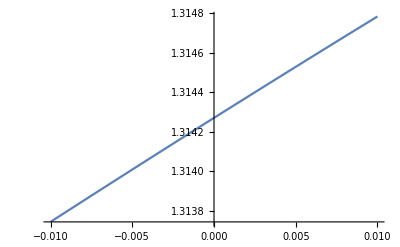

```mathematica
Plot[4*pudfinal[k,4], {k,-0.01,0.01}]
```

### Running the Algorithm for m1Um1Dm2U DIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode1,mode1, mode2, mode1, Stotal]
```

-(15 √π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (1-(((b^2 x1p)/(a-b)+5+1/(a-b))^2)/(3 (-2 a+b+b^2/(2 (a-b))))+(((b^2 x1p)/(a-b)+2 b x2+4+(b^2 x3p)/(a-b))^4)/(60 (-2 a+b+b^2/(2 1))^2)) (-(8 2^(3/4) a^(19/4) (a-3 b)^(3/2) b^2 (x1p-x2p) (-(4 2^(1/4) a^(7/4) x1p^2)/π^(3/4)+(4 2^(1/4) a^(7/4) x2p^2)/π^(3/4)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(8 2^(3/4) a^(19/4) (a-3 b)^(3/2) b^2 (x1p-x3p) ((4 2^(1/4) a^(7/4) x1p^2)/π^(3/4)-(4 2^(1/4) a^(7/4) x3p^2)/π^(3/4)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(8 2^(3/4) a^(19/4) (a-3 b)^(3/2) b^2 (x2p-x3p) (-(4 2^(1/4) a^(7/4) x2p^2)/π^(3/4)+(4 2^(1/4) a^(7/4) x3p^2)/π^(3/4)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(8 (2 a-b-b^2/(2 (a-b)))^(5/2) (-2 a+b+b^2/(2 (a-b))))+(3 √π (1-1^2/1+(1)^4/(12 1^2)) ((4 2^(3/4) a^(19/4) (1)^(3/2) b^2 x2 (x1p-x2p) (-(4 2^(1/4) a^(7/4) x1p^2)/π^(3/4)+(4 2^(1/4) a^1 x2p^2)/π^(3/4)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(4 6 x3)/(9 2 π^1)+24))/(4 (2 a-b-b^2/(2 (a-b)))^(5/2))-(3 √π (1) (1-1^2/(6 1)) (1))/(4 (2 a-b-1)^(3/2) (-2 a+b+b^2/(2 (a-b))))+(√π (1-1) (1))/(2 1^1)-(√π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (207+(8 8 (1))/(9 2 π^1)))/(2 √(2 a-b-b^2/(2 (a-b))) (-2 a+b+b^2/(2 (a-b))))+(√π (-(4 2^(3/4) a^(23/4) (a-3 b)^(3/2) x2^3 (x1p-x2p) (-(4 2^(1/4) a^(7/4) x1p^2)/π^(3/4)+(4 2^(1/4) a^(7/4) x2p^2)/π^(3/4)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+255))/(√(2 a-b-b^2/(2 (a-b))))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(9 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) (2 a^2-4 a b+b^2)^5 √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^2)2 √2 a^(9/2) (a-1)^(3/2) (6 b^10 (x1p^4+x2p^4+x2p^3 x3p-x2p^2 x3p^2+x2p x3p^3+x3p^4+x1p^3 (x2p+x3p)-x1p^2 (x2p+x3p)^2+x1p (x2p^3-2 x2p^2 x3p-2 x2p x3p^2+x3p^3))+16+8 a^6 b^4 (8 b^2 x1p^7 x3+8 b^2 x2p^7 x3+15+x1p^2 (196 b^2 x2p^5 x3+60 b x2p^4 (30+b x3 (24 x3+x3p))-4 b x2p^3 (2084 b x3^3+795 x3p+716 b x3^2 x3p+x3 (751+284 b x3p^2))+2 x2p^2 (897+32 b (71 x3^2+354 x3 x3p-180 x3p^2)+8 b^2 x3 (139 x3^3+4959 x3^2 x3p-606 x3 x3p^2-71 x3p^3))+x2p (-532 b^2 x3^5-4064 b^2 x3^4 x3p+4 x3p (664-795 b x3p^2)-16 b x3^2 x3p (-714+179 b x3p^2)+8 b x3^3 (-737+9918 b x3p^2)+3 x3 (-653+7552 b x3p^2+20 b^2 x3p^4))+x3p (-532 b^2 x3^5+2224 b^2 x3^4 x3p+32 b x3^2 x3p (142+45 b x3p^2)+6 x3p (299+300 b x3p^2)-8 b x3^3 (737+1042 b x3p^2)+x3 (-1959-3004 b x3p^2+196 b^2 x3p^4)))))
 |  |  |  |

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-((4 √2 a^(5/2) (a-3 b)^(3/2) (-178125 b^16+1875 a b^15 (1405+2 b (156 x2p^2-49 x2p x3+74 x3^2+312 x2p x3p-49 x3 x3p+156 x3p^2))+524288 a^19 x3^3 (x2p+x3p) (-2 x2p^2+2 b x2p^3 x3p-2 x3p^2+x2p x3p (3+2 b x3p^2))-125 a^2 b^14 (144660+5 b (10611 x2p^2-3808 x2p x3+7422 x3^2+20372 x2p x3p-3808 x3 x3p+10611 x3p^2)+4 b^2 (4819 x2p^4+1529 x3^4-1833 x3^3 x3p+1056 x3^2 x3p^2-3102 x3 x3p^3+4819 x3p^4+x2p^3 (-3102 x3+8276 x3p)+x2p^2 (1056 x3^2-1181 x3 x3p+6789 x3p^2)+x2p (-1833 x3^3+2112 x3^2 x3p-1181 x3 x3p^2+8276 x3p^3)))-131072 a^18 x3 (4 b^2 x2p^5 x3^2-2 x3p^3+8 b^2 x3^3 x3p^4+x3^2 x3p (-1-164 b x3p^2+4 b^2 x3p^4)+2 b x2p^4 (x3p+4 b x3^2 (x3+21 x3p))+x2p^2 x3p (1+4 b^2 x3^2 x3p (-2 x3+43 x3p)+2 b (43 x3^2+x3p^2))+2 x2p^3 (-1+86 b^2 x3^2 x3p^2+b (-82 x3^2+2 x3 x3p+x3p^2))+x2p (x3p^2+4 b x3 x3p^3+2 b x3p^4+x3^2 (-1+86 b x3p^2+168 b^2 x3p^4)))+32768 a^17 (4 b^2 x2p^5 x3 (1+2 b x3 (36 x3-x3p))+4 b^2 x2p^4 x3 (142 b x3^3+43 x3p+1616 b x3^2 x3p+x3 (8-4 b x3p^2))-4 b x2p^3 (4 b^2 x3^5-x3p+4 b^2 x3^4 x3p+x3 (42-44 b x3p^2)+b x3^2 x3p (-81+4 b x3p^2)-6 b x3^3 (-257+282 b x3p^2))+x3 x3p (-1-8 b^3 x3^2 x3p^2 (2 x3^2-71 x3 x3p-36 x3p^2)-84 b (x3^2+2 x3p^2)+4 b^2 x3p (3 x3^3-1542 x3^2 x3p+8 x3 x3p^2+x3p^3))+4 b x2p^2 x3 (22 x3p+2 b^2 x3 x3p (x3^3-74 x3^2 x3p+846 x3 x3p^2-2 x3p^3)+b (3 x3^3+865 x3^2 x3p-2 x3 x3p^2+44 x3p^3))+x2p (8 b^3 x3^5 x3p^2+4 b x3p^3-16 b^3 x3^4 x3p^3+4 b x3^2 x3p (2+81 b x3p^2-2 b^2 x3p^4)+x3 (-1+88 b x3p^2+172 b^2 x3p^4)+4 b x3^3 (-21+865 b x3p^2+1616 b^2 x3p^4)))+16384 a^16 b (43 x2p x3-4 x2p x3p+43 x3 x3p+8 b^3 x3^2 (x2p^6-7 x2p^5 (84 x3-5 x3p)+x2p^4 (-1148 x3^2-9429 x3 x3p+69 x3p^2)+x3p^3 (67 x3^3-1148 x3^2 x3p-588 x3 x3p^2+x3p^3)+x2p x3p^2 (-32 x3^3+70 x3^2 x3p-9429 x3 x3p^2+35 x3p^3)+x2p^2 x3p (-32 x3^3+1254 x3^2 x3p-10079 x3 x3p^2+69 x3p^3)+x2p^3 (67 x3^3+70 x3^2 x3p-10079 x3 x3p^2+70 x3p^3))-2 b (22 x2p^4+12 x3^4-796 x3^3 x3p+17 x3^2 x3p^2-1604 x3 x3p^3+22 x3p^4+x2p^3 (-1604 x3+83 x3p)+x2p^2 (17 x3^2+898 x3 x3p-16 x3p^2)+x2p (-796 x3^3+166 x3^2 x3p+898 x3 x3p^2+83 x3p^3))-4 b^2 (x2p^5 (37 x3-5 x3p)+2 x2p^4 (137 x3^2+420 x3 x3p-5 x3p^2)+x2p^3 (-17640 x3^3+1495 x3^2 x3p+879 x3 x3p^2-10 x3p^3)+x2p^2 (98 x3^4+10788 x3^3 x3p-70 x3^2 x3p^2+879 x3 x3p^3-10 x3p^4)+x3 x3p (-x3^4+98 x3^3 x3p-17640 x3^2 x3p^2+274 x3 x3p^3+37 x3p^4)-x2p (x3^5+8 x3^4 x3p-10788 x3^3 x3p^2-1495 x3^2 x3p^3-840 x3 x3p^4+5 x3p^5)))+4096 a^14 b^2 (-36-b (981 x2p^2-9488 x2p x3+1188 x3^2+3242 x2p x3p-9488 x3 x3p+981 x3p^2)-2 b^2 (11422 x2p^4+6108 x3^4-68879 x3^3 x3p+8919 x3^2 x3p^2-144518 x3 x3p^3+11422 x3p^4+x2p^3 (-144518 x3+17077 x3p)+x2p^2 (8919 x3^2+97836 x3 x3p-9462 x3p^2)+x2p (-68879 x3^3+35518 x3^2 x3p+97836 x3 x3p^2+17077 x3p^3))+8 b^4 x3 (x2p^7+x2p^6 (349 x3+36 x3p)+x2p^5 (-37956 x3^2+4984 x3 x3p+104 x3p^2)+x2p^4 (-73721 x3^3-421385 x3^2 x3p+9653 x3 x3p^2+139 x3p^3)+x2p^3 (9088 x3^4+9723 x3^3 x3p-465103 x3^2 x3p^2+10036 x3 x3p^3+139 x3p^4)+x3p^2 (-24 x3^5+9088 x3^4 x3p-73721 x3^3 x3p^2-37956 x3^2 x3p^3+349 x3 x3p^4+x3p^5)+x2p x3p (4 x3^5-4140 x3^4 x3p+9723 x3^3 x3p^2-421385 x3^2 x3p^3+4984 x3 x3p^4+36 x3p^5)+x2p^2 (-24 x3^5-4140 x3^4 x3p+88528 x3^3 x3p^2-465103 x3^2 x3p^3+9653 x3 x3p^4+104 x3p^5))+4 b^3 (145 x2p^6-6 x3^6+581 x3^5 x3p-12128 x3^4 x3p^2+770642 x3^3 x3p^3-39468 x3^2 x3p^4-6029 x3 x3p^5+145 x3p^6+x2p^5 (-6029 x3+2910 x3p)+x2p^4 (-39468 x3^2-78158 x3 x3p+5685 x3p^2)+x2p^3 (770642 x3^3-124603 x3^2 x3p-85143 x3 x3p^2+5840 x3p^3)+x2p^2 (-12128 x3^4-586922 x3^3 x3p+11978 x3^2 x3p^2-85143 x3 x3p^3+5685 x3p^4)+x2p (581 x3^5+4698 x3^4 x3p-586922 x3^3 x3p^2-124603 x3^2 x3p^3-78158 x3 x3p^4+2910 x3p^5)))-10 a^3 b^13 (-7619625-50 b (71373 x2p^2-28872 x2p x3+69582 x3^2+128996 x2p x3p-28872 x3 x3p+71373 x3p^2)-50 b^2 (62342 x2p^4+21718 x3^4-22563 x3^3 x3p+23030 x3^2 x3p^2-48523 x3 x3p^3+62342 x3p^4+x2p^3 (-48523 x3+80343 x3p)+2 x2p^2 (11515 x3^2-547 x3 x3p+16251 x3p^2)+x2p (-22563 x3^3+48210 x3^2 x3p-1094 x3 x3p^2+80343 x3p^3))+16 b^3 (1126 x2p^6-61 x3^6+1558 x3^5 x3p-13385 x3^4 x3p^2+43965 x3^3 x3p^3+2435 x3^2 x3p^4-7512 x3 x3p^5+1126 x3p^6+x2p^5 (-7512 x3+3006 x3p)+5 x2p^4 (487 x3^2-3887 x3 x3p-2372 x3p^2)+15 x2p^3 (2931 x3^3+691 x3^2 x3p-8 x3 x3p^2-1832 x3p^3)-5 x2p^2 (2677 x3^4-5129 x3^3 x3p-9047 x3^2 x3p^2+24 x3 x3p^3+2372 x3p^4)+x2p (1558 x3^5-26770 x3^4 x3p+25645 x3^3 x3p^2+10365 x3^2 x3p^3-19435 x3 x3p^4+3006 x3p^5)))+4 a^4 b^12 (-54883500-125 b (250542 x2p^2-115865 x2p x3+312942 x3^2+421334 x2p x3p-115865 x3 x3p+250542 x3p^2)-50 b^2 (946571 x2p^4+361616 x3^4-326912 x3^3 x3p+443984 x3^2 x3p^2-844733 x3 x3p^3+946571 x3p^4+x2p^3 (-844733 x3+851034 x3p)+x2p^2 (443984 x3^2+390301 x3 x3p-282574 x3p^2)+x2p (-326912 x3^3+949468 x3^2 x3p+390301 x3 x3p^2+851034 x3p^3))+16 b^4 (x2p-7 x3+x3p)^2 (87 x2p^6+3 x3^6-29 x3^5 x3p+5 x3^4 x3p^2+1055 x3^3 x3p^3-2455 x3^2 x3p^4-674 x3 x3p^5+87 x3p^6+x2p^5 (-674 x3+522 x3p)-5 x2p^4 (491 x3^2+299 x3 x3p-636 x3p^2)+5 x2p^3 (211 x3^3-964 x3^2 x3p+777 x3 x3p^2+1098 x3p^3)+5 x2p^2 (x3^4+258 x3^3 x3p-1321 x3^2 x3p^2+777 x3 x3p^3+636 x3p^4)+x2p (-29 x3^5+10 x3^4 x3p+1290 x3^3 x3p^2-4820 x3^2 x3p^3-1495 x3 x3p^4+522 x3p^5))+20 b^3 (35025 x2p^6-2342 x3^6-2 x2p^5 (70147 x3-77950 x3p)+20180 x3^5 x3p-230605 x3^4 x3p^2+1250240 x3^3 x3p^3-137560 x3^2 x3p^4-140294 x3 x3p^5+35025 x3p^6-5 x2p^4 (27512 x3^2+67494 x3 x3p+12075 x3p^2)+10 x2p^3 (125024 x3^3-34099 x3^2 x3p+34281 x3 x3p^2-36250 x3p^3)-5 x2p^2 (46121 x3^4+906 x3^3 x3p-92128 x3^2 x3p^2-68562 x3 x3p^3+12075 x3p^4)+10 x2p (2018 x3^5-40046 x3^4 x3p-453 x3^3 x3p^2-34099 x3^2 x3p^3-33747 x3 x3p^4+15590 x3p^5)))-16384 a^15 b^2 (-4 b^3 x3^6 x3p^2+2 b^2 x3^5 x3p (37+2022 b x3p^2)+8 b x3^3 x3p (1130+34326 b x3p^2-2885 b^2 x3p^4)+2 x3 x3p (207+9253 b x3p^2-612 b^2 x3p^4)+x3p^2 (-15-743 b x3p^2+10 b^2 x3p^4)-2 b x3^4 (201+1424 b x3p^2+22406 b^2 x3p^4)+2 x3^2 (-9-290 b x3p^2-4248 b^2 x3p^4+56 b^3 x3p^6)+2 b^2 x2p^6 (5+2 b x3 (28 x3+x3p))-4 b^2 x2p^5 (5770 b x3^3-90 x3p-545 b x3^2 x3p+x3 (306-3 b x3p^2))-b x2p^4 (743+2 b (4248 x3^2+9879 x3 x3p-355 x3p^2)+4 b^2 x3 (11203 x3^3+74506 x3^2 x3p-1064 x3 x3p^2-4 x3p^3))+2 b x2p^3 (2022 b^2 x3^5+2166 b^2 x3^4 x3p+x3p (-773+360 b x3p^2)+2 b x3^2 x3p (-8319+1094 b x3p^2)-8 b x3^3 (-17163+20273 b x3p^2)+x3 (9253-10561 b x3p^2+8 b^2 x3p^4))-x2p^2 (15+5 b (116 x3^2+2259 x3 x3p-114 x3p^2)+2 b^2 (1424 x3^4+93088 x3^3 x3p-1160 x3^2 x3p^2+10561 x3 x3p^3-355 x3p^4)+4 b^3 x3 (x3^5+468 x3^4 x3p-12852 x3^3 x3p^2+81092 x3^2 x3p^3-1064 x3 x3p^4-3 x3p^5))+x2p (2 b^2 x3^5 (37-936 b x3p^2)+4 b^2 x3^4 x3p (146+1083 b x3p^2)+x3p (-85-1546 b x3p^2+360 b^2 x3p^4)+4 b x3^2 x3p (-783-8319 b x3p^2+545 b^2 x3p^4)-8 b x3^3 (-1130+23272 b x3p^2+37253 b^2 x3p^4)+x3 (414-11295 b x3p^2-19758 b^2 x3p^4+4 b^3 x3p^6)))-2048 a^13 b^3 (-1143-2 b (7221 x2p^2-36281 x2p x3+8868 x3^2+18317 x2p x3p-36281 x3 x3p+7221 x3p^2)-2 b^2 (105824 x2p^4+55776 x3^4-373482 x3^3 x3p+81911 x3^2 x3p^2-810645 x3 x3p^3+105824 x3p^4+x2p^3 (-810645 x3+124581 x3p)+x2p^2 (81911 x3^2+616705 x3 x3p-96526 x3p^2)+x2p (-373482 x3^3+270172 x3^2 x3p+616705 x3 x3p^2+124581 x3p^3))+4 b^3 (1893 x2p^6-148 x3^6+5166 x3^5 x3p-67124 x3^4 x3p^2+3225388 x3^3 x3p^3-245202 x3^2 x3p^4-39676 x3 x3p^5+1893 x3p^6+x2p^5 (-39676 x3+27959 x3p)+x2p^4 (-245202 x3^2-440169 x3 x3p+54211 x3p^2)+x2p^3 (3225388 x3^3-664194 x3^2 x3p-486195 x3 x3p^2+56290 x3p^3)+x2p^2 (-67124 x3^4-2783666 x3^3 x3p+84904 x3^2 x3p^2-486195 x3 x3p^3+54211 x3p^4)+x2p (5166 x3^5+44102 x3^4 x3p-2783666 x3^3 x3p^2-664194 x3^2 x3p^3-440169 x3 x3p^4+27959 x3p^5))+8 b^4 (x2p^7 (28 x3-x3p)+x2p^6 (2556 x3^2+566 x3 x3p-4 x3p^2)+x2p^5 (-176748 x3^3+29729 x3^2 x3p+1588 x3 x3p^2-7 x3p^3)-2 x2p^4 (173116 x3^4+878831 x3^3 x3p-28512 x3^2 x3p^2-1065 x3 x3p^3+4 x3p^4)+x2p^3 (54257 x3^5+55702 x3^4 x3p-1955538 x3^3 x3p^2+59702 x3^2 x3p^3+2130 x3 x3p^4-7 x3p^5)-x3 x3p (x3^6+240 x3^5 x3p-54257 x3^4 x3p^2+346232 x3^3 x3p^3+176748 x3^2 x3p^4-2556 x3 x3p^5-28 x3p^6)-2 x2p^2 (120 x3^6+12312 x3^5 x3p-215186 x3^4 x3p^2+977769 x3^3 x3p^3-28512 x3^2 x3p^4-794 x3 x3p^5+2 x3p^6)-x2p (x3^7-112 x3^6 x3p+24624 x3^5 x3p^2-55702 x3^4 x3p^3+1757662 x3^3 x3p^4-29729 x3^2 x3p^5-566 x3 x3p^6+x3p^7)))-2048 a^12 b^4 (8268+b (63345 x2p^2-196797 x2p x3+79389 x3^2+136855 x2p x3p-196797 x3 x3p+63345 x3p^2)+b^2 (659580 x2p^4+341932 x3^4-1491615 x3^3 x3p+501886 x3^2 x3p^2-3381567 x3 x3p^3+659580 x3p^4+x2p^3 (-3381567 x3+633005 x3p)+x2p^2 (501886 x3^2+2913199 x3 x3p-671460 x3p^2)+x2p (-1491615 x3^3+1458612 x3^2 x3p+2913199 x3 x3p^2+633005 x3p^3))+b^3 (-29368 x2p^6+3176 x3^6+x2p^5 (370174 x3-355738 x3p)-58084 x3^5 x3p+505648 x3^4 x3p^2-20539484 x3^3 x3p^3+2152404 x3^2 x3p^4+370174 x3 x3p^5-29368 x3p^6+4 x2p^4 (538101 x3^2+910040 x3 x3p-171060 x3p^2)+x2p^3 (-20539484 x3^3+5203786 x3^2 x3p+4041710 x3 x3p^2-715740 x3p^3)+x2p^2 (505648 x3^4+20151148 x3^3 x3p-859036 x3^2 x3p^2+4041710 x3 x3p^3-684240 x3p^4)+x2p (-58084 x3^5-537824 x3^4 x3p+20151148 x3^3 x3p^2+5203786 x3^2 x3p^3+3640160 x3 x3p^4-355738 x3p^5))+4 b^4 (x2p^8+x2p^7 (-338 x3+29 x3p)+x2p^6 (-12225 x3^2-5117 x3 x3p+108 x3p^2)+x2p^5 (599295 x3^3-121297 x3^2 x3p-14045 x3 x3p^2+187 x3p^3)+x2p^4 (1198245 x3^4+5487276 x3^3 x3p-228877 x3^2 x3p^2-18916 x3 x3p^3+214 x3p^4)-x2p^3 (227177 x3^5+209123 x3^4 x3p-6097885 x3^3 x3p^2+239610 x3^2 x3p^3+18916 x3 x3p^4-187 x3p^5)+x2p^2 (1268 x3^6+103106 x3^5 x3p-1506572 x3^4 x3p^2+6097885 x3^3 x3p^3-228877 x3^2 x3p^4-14045 x3 x3p^5+108 x3p^6)+x3p (29 x3^7+1268 x3^6 x3p-227177 x3^5 x3p^2+1198245 x3^4 x3p^3+599295 x3^3 x3p^4-12225 x3^2 x3p^5-338 x3 x3p^6+x3p^7)+x2p (29 x3^7-1344 x3^6 x3p+103106 x3^5 x3p^2-209123 x3^4 x3p^3+5487276 x3^3 x3p^4-121297 x3^2 x3p^5-5117 x3 x3p^6+29 x3p^7)))+512 a^11 b^5 (144375+2 b (369426 x2p^2-784899 x2p x3+476064 x3^2+715477 x2p x3p-784899 x3 x3p+369426 x3p^2)+2 b^2 (2924247 x2p^4+1488734 x3^4-4480997 x3^3 x3p+2171007 x3^2 x3p^2-10713080 x3 x3p^3+2924247 x3p^4+x2p^3 (-10713080 x3+2304683 x3p)+x2p^2 (2171007 x3^2+10464830 x3 x3p-3341628 x3p^2)+x2p (-4480997 x3^3+5773244 x3^2 x3p+10464830 x3 x3p^2+2304683 x3p^3))-4 b^3 (75179 x2p^6-9736 x3^6+108519 x3^5 x3p-659746 x3^4 x3p^2+25162662 x3^3 x3p^3-3436844 x3^2 x3p^4-632591 x3 x3p^5+75179 x3p^6+x2p^5 (-632591 x3+789244 x3p)+x2p^4 (-3436844 x3^2-5611810 x3 x3p+1501165 x3p^2)+x2p^3 (25162662 x3^3-7633276 x3^2 x3p-6174175 x3 x3p^2+1574200 x3p^3)+x2p^2 (-659746 x3^4-27952644 x3^3 x3p+1570336 x3^2 x3p^2-6174175 x3 x3p^3+1501165 x3p^4)+x2p (108519 x3^5+1119238 x3^4 x3p-27952644 x3^3 x3p^2-7633276 x3^2 x3p^3-5611810 x3 x3p^4+789244 x3p^5))+8 b^4 (20 x2p^8-2 x3^8+344 x3^7 x3p+3554 x3^6 x3p^2-687068 x3^5 x3p^3+3110940 x3^4 x3p^4+1497112 x3^3 x3p^5-40140 x3^2 x3p^6-2314 x3 x3p^7+20 x3p^8+x2p^7 (-2314 x3+351 x3p)+x2p^6 (-40140 x3^2-29473 x3 x3p+1246 x3p^2)+x2p^5 (1497112 x3^3-344515 x3^2 x3p-79559 x3 x3p^2+2145 x3p^3)+10 x2p^4 (311094 x3^4+1286561 x3^3 x3p-62982 x3^2 x3p^2-10751 x3 x3p^3+246 x3p^4)-x2p^3 (687068 x3^5+495505 x3^4 x3p-14077250 x3^3 x3p^2+650890 x3^2 x3p^3+107510 x3 x3p^4-2145 x3p^5)+x2p^2 (3554 x3^6+307834 x3^5 x3p-3793690 x3^4 x3p^2+14077250 x3^3 x3p^3-629820 x3^2 x3p^4-79559 x3 x3p^5+1246 x3p^6)+x2p (344 x3^7-9082 x3^6 x3p+307834 x3^5 x3p^2-495505 x3^4 x3p^3+12865610 x3^3 x3p^4-344515 x3^2 x3p^5-29473 x3 x3p^6+351 x3p^7)))-512 a^10 b^6 (424710+5 b (302817 x2p^2-470621 x2p x3+404499 x3^2+540959 x2p x3p-470621 x3 x3p+302817 x3p^2)+b^2 (9512481 x2p^4+4748656 x3^4-10259912 x3^3 x3p+6843259 x3^2 x3p^2-26096853 x3 x3p^3+9512481 x3p^4+x2p^3 (-26096853 x3+6113999 x3p)+x2p^2 (6843259 x3^2+28713341 x3 x3p-12152714 x3p^2)+x2p (-10259912 x3^3+17072918 x3^2 x3p+28713341 x3 x3p^2+6113999 x3p^3))-2 b^3 (266631 x2p^6-37674 x3^6+274539 x3^5 x3p-1196245 x3^4 x3p^2+47704320 x3^3 x3p^3-8102120 x3^2 x3p^4-1611014 x3 x3p^5+266631 x3p^6+x2p^5 (-1611014 x3+2503016 x3p)-5 x2p^4 (1620424 x3^2+2590137 x3 x3p-935427 x3p^2)+5 x2p^3 (9540864 x3^3-3390397 x3^2 x3p-2757147 x3 x3p^2+976300 x3p^3)-5 x2p^2 (239249 x3^4+11837300 x3^3 x3p-827254 x3^2 x3p^2+2757147 x3 x3p^3-935427 x3p^4)+x2p (274539 x3^5+3240940 x3^4 x3p-59186500 x3^3 x3p^2-16951985 x3^2 x3p^3-12950685 x3 x3p^4+2503016 x3p^5))+4 b^4 (169 x2p^8-34 x3^8+2213 x3^7 x3p+3381 x3^6 x3p^2-1523939 x3^5 x3p^3+6109230 x3^4 x3p^4+2751407 x3^3 x3p^5-92676 x3^2 x3p^6-9911 x3 x3p^7+169 x3p^8+x2p^7 (-9911 x3+2336 x3p)+x2p^6 (-92676 x3^2-113059 x3 x3p+8016 x3p^2)+x2p^5 (2751407 x3^3-677816 x3^2 x3p-300931 x3 x3p^2+13744 x3p^3)+5 x2p^4 (1221846 x3^4+4498646 x3^3 x3p-232322 x3^2 x3p^2-81375 x3 x3p^3+3158 x3p^4)-x2p^3 (1523939 x3^5+589910 x3^4 x3p-23656895 x3^3 x3p^2+1152940 x3^2 x3p^3+406875 x3 x3p^4-13744 x3p^5)+x2p^2 (3381 x3^6+645140 x3^5 x3p-6697500 x3^4 x3p^2+23656895 x3^3 x3p^3-1161610 x3^2 x3p^4-300931 x3 x3p^5+8016 x3p^6)+x2p (2213 x3^7-38134 x3^6 x3p+645140 x3^5 x3p^2-589910 x3^4 x3p^3+22493230 x3^3 x3p^4-677816 x3^2 x3p^5-113059 x3 x3p^6+2336 x3p^7)))+8 a^5 b^11 (56986875+25 b (1635006 x2p^2-884619 x2p x3+2362344 x3^2+2586262 x2p x3p-884619 x3 x3p+1635006 x3p^2)+50 b^2 (1800453 x2p^4+744570 x3^4-625139 x3^3 x3p+967791 x3^2 x3p^2-1831838 x3 x3p^3+1800453 x3p^4+x2p^3 (-1831838 x3+1095337 x3p)+x2p^2 (967791 x3^2+1652386 x3 x3p-1674732 x3p^2)+x2p (-625139 x3^3+2102932 x3^2 x3p+1652386 x3 x3p^2+1095337 x3p^3))-4 b^3 (611539 x2p^6-52704 x3^6+148537 x3^5 x3p-2061315 x3^4 x3p^2+20950860 x3^3 x3p^3-4150110 x3^2 x3p^4-1859343 x3 x3p^5+611539 x3p^6+x2p^5 (-1859343 x3+3473609 x3p)-5 x2p^4 (830022 x3^2+1157468 x3 x3p-560617 x3p^2)+5 x2p^3 (4190172 x3^3-1997963 x3^2 x3p+729439 x3 x3p^2-23594 x3p^3)-5 x2p^2 (412263 x3^4+2480359 x3^3 x3p-631618 x3^2 x3p^2-729439 x3 x3p^3-560617 x3p^4)+x2p (148537 x3^5-2145130 x3^4 x3p-12401795 x3^3 x3p^2-9989815 x3^2 x3p^3-5787340 x3 x3p^4+3473609 x3p^5))+8 b^4 (836 x2p^8-1190 x3^8+14107 x3^7 x3p-15382 x3^6 x3p^2-582867 x3^5 x3p^3+1640760 x3^4 x3p^4+94115 x3^3 x3p^5-70096 x3^2 x3p^6-2299 x3 x3p^7+836 x3p^8+x2p^7 (-2299 x3+8413 x3p)-4 x2p^6 (17524 x3^2+12917 x3 x3p-4377 x3p^2)+x2p^5 (94115 x3^3-190826 x3^2 x3p-12404 x3 x3p^2+7691 x3p^3)+5 x2p^4 (328152 x3^4+114415 x3^3 x3p-56238 x3^2 x3p^2+41007 x3 x3p^3-896 x3p^4)+x2p^3 (-582867 x3^5+2468915 x3^4 x3p-2798100 x3^3 x3p^2-320920 x3^2 x3p^3+205035 x3 x3p^4+7691 x3p^5)-2 x2p^2 (7691 x3^6+221463 x3^5 x3p-1475655 x3^4 x3p^2+1399050 x3^3 x3p^3+140595 x3^2 x3p^4+6202 x3 x3p^5-8754 x3p^6)+x2p (14107 x3^7-38114 x3^6 x3p-442926 x3^5 x3p^2+2468915 x3^4 x3p^3+572075 x3^3 x3p^4-190826 x3^2 x3p^5-51668 x3 x3p^6+8413 x3p^7)))+128 a^9 b^7 (3561645+10 b (900273 x2p^2-1074567 x2p x3+1255308 x3^2+1510171 x2p x3p-1074567 x3 x3p+900273 x3p^2)+10 b^2 (4619531 x2p^4+2256192 x3^4-3613895 x3^3 x3p+3199336 x3^2 x3p^2-9838569 x3 x3p^3+4619531 x3p^4+x2p^3 (-9838569 x3+2403829 x3p)+x2p^2 (3199336 x3^2+11980923 x3 x3p-6487404 x3p^2)+x2p (-3613895 x3^3+7620942 x3^2 x3p+11980923 x3 x3p^2+2403829 x3p^3))-4 b^3 (668119 x2p^6-95896 x3^6+468417 x3^5 x3p-1525520 x3^4 x3p^2+70046040 x3^3 x3p^3-14148190 x3^2 x3p^4-3071887 x3 x3p^5+668119 x3p^6+x2p^5 (-3071887 x3+5709589 x3p)-5 x2p^4 (2829638 x3^2+4442322 x3 x3p-2072157 x3p^2)+5 x2p^3 (14009208 x3^3-5725442 x3^2 x3p-4385979 x3 x3p^2+2127726 x3p^3)-5 x2p^2 (305104 x3^4+18871496 x3^3 x3p-1544792 x3^2 x3p^2+4385979 x3 x3p^3-2072157 x3p^4)+x2p (468417 x3^5+6491360 x3^4 x3p-94357480 x3^3 x3p^2-28627210 x3^2 x3p^3-22211610 x3 x3p^4+5709589 x3p^5))+8 b^4 (781 x2p^8-234 x3^8+8552 x3^7 x3p-9796 x3^6 x3p^2-2491928 x3^5 x3p^3+9074505 x3^4 x3p^4+3662916 x3^3 x3p^5-152282 x3^2 x3p^6-27514 x3 x3p^7+781 x3p^8+x2p^7 (-27514 x3+9392 x3p)+x2p^6 (-152282 x3^2-292391 x3 x3p+31382 x3p^2)+x2p^5 (3662916 x3^3-898477 x3^2 x3p-766609 x3 x3p^2+53496 x3p^3)+5 x2p^4 (1814901 x3^4+5750798 x3^3 x3p-266474 x3^2 x3p^2-206094 x3 x3p^3+12290 x3p^4)+x2p^3 (-2491928 x3^5+329155 x3^4 x3p+27782790 x3^3 x3p^2-1172350 x3^2 x3p^3-1030470 x3 x3p^4+53496 x3p^5)+x2p^2 (-9796 x3^6+895543 x3^5 x3p-7692100 x3^4 x3p^2+27782790 x3^3 x3p^3-1332370 x3^2 x3p^4-766609 x3 x3p^5+31382 x3p^6)+x2p (8552 x3^7-103346 x3^6 x3p+895543 x3^5 x3p^2+329155 x3^4 x3p^3+28753990 x3^3 x3p^4-898477 x3^2 x3p^5-292391 x3 x3p^6+9392 x3p^7)))-128 a^8 b^8 (5489220+5 b (1981200 x2p^2-1882717 x2p x3+2890749 x3^2+3165025 x2p x3p-1882717 x3 x3p+1981200 x3p^2)+5 b^2 (8440986 x2p^4+4016830 x3^4-9 x2p^3 (1597528 x3-403691 x3p)-4939947 x3^3 x3p+5589921 x3^2 x3p^2-14377752 x3 x3p^3+8440986 x3p^4+3 x2p^2 (1863307 x3^2+6243898 x3 x3p-4193428 x3p^2)+x2p (-4939947 x3^3+12875842 x3^2 x3p+18731694 x3 x3p^2+3633219 x3p^3))-2 b^3 (1182887 x2p^6-162282 x3^6+527861 x3^5 x3p-1528030 x3^4 x3p^2+79413630 x3^3 x3p^3-18170590 x3^2 x3p^4-4362834 x3 x3p^5+1182887 x3p^6+x2p^5 (-4362834 x3+9281147 x3p)-5 x2p^4 (3634118 x3^2+5556479 x3 x3p-3204721 x3p^2)+5 x2p^3 (15882726 x3^3-7330887 x3^2 x3p-4674853 x3 x3p^2+3170138 x3p^3)-5 x2p^2 (305606 x3^4+22067152 x3^3 x3p-1986962 x3^2 x3p^2+4674853 x3 x3p^3-3204721 x3p^4)+x2p (527861 x3^5+8643890 x3^4 x3p-110335760 x3^3 x3p^2-36654435 x3^2 x3p^3-27782395 x3 x3p^4+9281147 x3p^5))+4 b^4 (2126 x2p^8-842 x3^8+20641 x3^7 x3p-38708 x3^6 x3p^2-2991667 x3^5 x3p^3+10098875 x3^4 x3p^4+3412626 x3^3 x3p^5-180943 x3^2 x3p^6-49236 x3 x3p^7+2126 x3p^8+x2p^7 (-49236 x3+23388 x3p)+x2p^6 (-180943 x3^2-501827 x3 x3p+76158 x3p^2)+x2p^5 (3412626 x3^3-762633 x3^2 x3p-1286631 x3 x3p^2+128156 x3p^3)+5 x2p^4 (2019775 x3^4+5175101 x3^3 x3p-150679 x3^2 x3p^2-339082 x3 x3p^3+29304 x3p^4)+x2p^3 (-2991667 x3^5+2641075 x3^4 x3p+20698185 x3^3 x3p^2-343410 x3^2 x3p^3-1695410 x3 x3p^4+128156 x3p^5)+x2p^2 (-38708 x3^6+683939 x3^5 x3p-4389000 x3^4 x3p^2+20698185 x3^3 x3p^3-753395 x3^2 x3p^4-1286631 x3 x3p^5+76158 x3p^6)+x2p (20641 x3^7-181216 x3^6 x3p+683939 x3^5 x3p^2+2641075 x3^4 x3p^3+25875505 x3^3 x3p^4-762633 x3^2 x3p^5-501827 x3 x3p^6+23388 x3p^7)))-32 a^6 b^10 (21915150+25 b (830463 x2p^2-534768 x2p x3+1266189 x3^2+1276301 x2p x3p-534768 x3 x3p+830463 x3p^2)+5 b^2 (11951218 x2p^4+5256488 x3^4-4553616 x3^3 x3p+7025122 x3^2 x3p^2-14089129 x3 x3p^3+11951218 x3p^4+x2p^3 (-14089129 x3+5301747 x3p)+2 x2p^2 (3512561 x3^2+8398994 x3 x3p-7878846 x3p^2)+x2p (-4553616 x3^3+15503244 x3^2 x3p+16797988 x3 x3p^2+5301747 x3p^3))-2 b^3 (1192886 x2p^6+x2p^5 (-3440956 x3+7780816 x3p)-20 x2p^4 (533230 x3^2+732889 x3 x3p-512802 x3p^2)+5 x2p^3 (8981476 x3^3-4735755 x3^2 x3p-303712 x3 x3p^2+1467244 x3p^3)-5 x2p^2 (420258 x3^4+9423097 x3^3 x3p-1026830 x3^2 x3p^2+303712 x3 x3p^3-2051208 x3p^4)+x2p (217418 x3^5+1583420 x3^4 x3p-47115485 x3^3 x3p^2-23678775 x3^2 x3p^3-14657780 x3 x3p^4+7780816 x3p^5)-2 (63364 x3^6-108709 x3^5 x3p+1050645 x3^4 x3p^2-22453690 x3^3 x3p^3+5332300 x3^2 x3p^4+1720478 x3 x3p^5-596443 x3p^6))+4 b^4 (2848 x2p^8-1966 x3^8+28343 x3^7 x3p-44773 x3^6 x3p^2-1554076 x3^5 x3p^3+4653080 x3^4 x3p^4+720723 x3^3 x3p^5-119949 x3^2 x3p^6-29846 x3 x3p^7+2848 x3p^8+x2p^7 (-29846 x3+28459 x3p)+x2p^6 (-119949 x3^2-315247 x3 x3p+83294 x3p^2)+x2p^5 (720723 x3^3-217944 x3^2 x3p-680641 x3 x3p^2+122613 x3p^3)+5 x2p^4 (930616 x3^4+1013673 x3^3 x3p+11403 x3^2 x3p^2-134922 x3 x3p^3+25972 x3p^4)+x2p^3 (-1554076 x3^5+4740195 x3^4 x3p-2171270 x3^3 x3p^2+310020 x3^2 x3p^3-674610 x3 x3p^4+122613 x3p^5)+x2p^2 (-44773 x3^6-518453 x3^5 x3p+4332480 x3^4 x3p^2-2171270 x3^3 x3p^3+57015 x3^2 x3p^4-680641 x3 x3p^5+83294 x3p^6)+x2p (28343 x3^7-126646 x3^6 x3p-518453 x3^5 x3p^2+4740195 x3^4 x3p^3+5068365 x3^3 x3p^4-217944 x3^2 x3p^5-315247 x3 x3p^6+28459 x3p^7)))+32 a^7 b^9 (25292325+10 b (3279576 x2p^2-2544734 x2p x3+4964604 x3^2+5073527 x2p x3p-2544734 x3 x3p+3279576 x3p^2)+10 b^2 (11616376 x2p^4+5346232 x3^4-5307836 x3^3 x3p+7294451 x3^2 x3p^2-16251885 x3 x3p^3+11616376 x3p^4+x2p^3 (-16251885 x3+4582229 x3p)+x2p^2 (7294451 x3^2+21331195 x3 x3p-17240794 x3p^2)+x2p (-5307836 x3^3+16396552 x3^2 x3p+21331195 x3 x3p^2+4582229 x3p^3))-4 b^3 (1453541 x2p^6-180284 x3^6+388428 x3^5 x3p-1660090 x3^4 x3p^2+68929170 x3^3 x3p^3-16801720 x3^2 x3p^4-4555193 x3 x3p^5+1453541 x3p^6+x2p^5 (-4555193 x3+10467246 x3p)-5 x2p^4 (3360344 x3^2+4907718 x3 x3p-3305423 x3p^2)+5 x2p^3 (13785834 x3^3-6996026 x3^2 x3p-2827461 x3 x3p^2+3005364 x3p^3)-5 x2p^2 (332018 x3^4+18052873 x3^3 x3p-1705636 x3^2 x3p^2+2827461 x3 x3p^3-3305423 x3p^4)+x2p (388428 x3^5+6766570 x3^4 x3p-90264365 x3^3 x3p^2-34980130 x3^2 x3p^3-24538590 x3 x3p^4+10467246 x3p^5))+8 b^4 (3385 x2p^8-1710 x3^8+31148 x3^7 x3p-58721 x3^6 x3p^2-2592185 x3^5 x3p^3+8221125 x3^4 x3p^4+2080340 x3^3 x3p^5-162819 x3^2 x3p^6-53707 x3 x3p^7+3385 x3p^8+x2p^7 (-53707 x3+35095 x3p)-3 x2p^6 (54273 x3^2+180243 x3 x3p-36790 x3p^2)+x2p^5 (2080340 x3^3-408639 x3^2 x3p-1325997 x3 x3p^2+179785 x3p^3)+5 x2p^4 (1644225 x3^4+3052535 x3^3 x3p+1763 x3^2 x3p^2-330059 x3 x3p^3+40450 x3p^4)-5 x2p^3 (518437 x3^5-973270 x3^4 x3p-1387815 x3^3 x3p^2-101854 x3^2 x3p^3+330059 x3 x3p^4-35957 x3p^5)+x2p^2 (-58721 x3^6+6190 x3^5 x3p+1349450 x3^4 x3p^2+6939075 x3^3 x3p^3+8815 x3^2 x3p^4-1325997 x3 x3p^5+110370 x3p^6)+x2p (31148 x3^7-199282 x3^6 x3p+6190 x3^5 x3p^2+4866350 x3^4 x3p^3+15262675 x3^3 x3p^4-408639 x3^2 x3p^5-540729 x3 x3p^6+35095 x3p^7)))))/(9 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (4 a^2-10 a b+5 b^2)^8 √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(a^(5/2) (a-3 b)^(3/2) (183312 b^16+16384 a^19 x3^3 x3p^3+1024 a^17 x3 x3p (1+102 b (x3^2+x3p^2)-12 b^2 x3 x3p (x3^2-386 x3 x3p+x3p^2)+8 b^3 x3^2 x3p^2 (x3^2-44 x3 x3p+x3p^2))-32 a b^15 (64965+b (6195 x3^2-4138 x3 x3p+6195 x3p^2))+4096 a^18 (-x3 x3p^3+4 b^2 x3^4 x3p^4-x3^3 (x3p+100 b x3p^3))-1024 a^16 b (26 x3 x3p+12 b^3 x3^3 x3p^3 (14 x3^2-297 x3 x3p+14 x3p^2)+b (-10 x3^4+1198 x3^3 x3p-11 x3^2 x3p^2+1198 x3 x3p^3-10 x3p^4)+2 b^2 x3 x3p (x3^4-125 x3^3 x3p+16488 x3^2 x3p^2-125 x3 x3p^3+x3p^4))+8 a^2 b^14 (1352871+b (330366 x3^2-271844 x3 x3p+330366 x3p^2)+b^2 (113225 x3^4-100604 x3^3 x3p+87670 x3^2 x3p^2-100604 x3 x3p^3+113225 x3p^4))+128 a^14 b^2 (27+2 b (489 x3^2-8989 x3 x3p+489 x3p^2)+8 b^4 x3^2 x3p^2 (31 x3^4-9216 x3^3 x3p+92641 x3^2 x3p^2-9216 x3 x3p^3+31 x3p^4)+2 b^2 (8025 x3^4-169571 x3^3 x3p+8705 x3^2 x3p^2-169571 x3 x3p^3+8025 x3p^4)+4 b^3 (5 x3^6-858 x3^5 x3p+27349 x3^4 x3p^2-1154194 x3^3 x3p^3+27349 x3^2 x3p^4-858 x3 x3p^5+5 x3p^6))-64 a^13 b^3 (1074+b (18234 x3^2-178043 x3 x3p+18234 x3p^2)+2 b^2 (93778 x3^4-1214007 x3^3 x3p+100092 x3^2 x3p^2-1214007 x3 x3p^3+93778 x3p^4)+8 b^4 x3 x3p (x3^6+420 x3^5 x3p-71074 x3^4 x3p^2+562020 x3^3 x3p^3-71074 x3^2 x3p^4+420 x3 x3p^5+x3p^6)+4 b^3 (161 x3^6-9856 x3^5 x3p+212130 x3^4 x3p^2-6221876 x3^3 x3p^3+212130 x3^2 x3p^4-9856 x3 x3p^5+161 x3p^6))+16 a^12 b^4 (39309+6 b (68699 x3^2-425848 x3 x3p+68699 x3p^2)+8 b^2 (372518 x3^4-3268711 x3^3 x3p+388803 x3^2 x3p^2-3268711 x3 x3p^3+372518 x3p^4)+16 b^4 x3 x3p (32 x3^6+3243 x3^5 x3p-388226 x3^4 x3p^2+2533431 x3^3 x3p^3-388226 x3^2 x3p^4+3243 x3 x3p^5+32 x3p^6)+8 b^3 (2316 x3^6-74523 x3^5 x3p+1171441 x3^4 x3p^2-25800480 x3^3 x3p^3+1171441 x3^2 x3p^4-74523 x3 x3p^5+2316 x3p^6))-8 a^3 b^13 (4284249+9 b (215671 x3^2-210322 x3 x3p+215671 x3p^2)+b^2 (1266675 x3^4-1381812 x3^3 x3p+912818 x3^2 x3p^2-1381812 x3 x3p^3+1266675 x3p^4)+b^3 (6085 x3^6+5518 x3^5 x3p-22709 x3^4 x3p^2-449788 x3^3 x3p^3-22709 x3^2 x3p^4+5518 x3 x3p^5+6085 x3p^6))+a^4 b^12 (73749057+b (53806308 x3^2-60957368 x3 x3p+53806308 x3p^2)-b^4 (11 x3^2-122 x3 x3p+11 x3p^2)^2 (15 x3^4+28 x3^3 x3p-230 x3^2 x3p^2+28 x3 x3p^3+15 x3p^4)+b^2 (51760906 x3^4-69297240 x3^3 x3p+37435196 x3^2 x3p^2-69297240 x3 x3p^3+51760906 x3p^4)+4 b^3 (118723 x3^6-61310 x3^5 x3p+188717 x3^4 x3p^2-12103460 x3^3 x3p^3+188717 x3^2 x3p^4-61310 x3 x3p^5+118723 x3p^6))-256 a^15 b^2 (8 b^3 x3^6 x3p^2+4 x3p^2 (6+209 b x3p^2)-16 b^2 x3^5 x3p (11+401 b x3p^2)-x3 x3p (1239+34436 b x3p^2+176 b^2 x3p^4)-4 b x3^3 x3p (8609+161521 b x3p^2+1604 b^2 x3p^4)+4 b x3^4 (209+2378 b x3p^2+22012 b^2 x3p^4)+4 x3^2 (6+229 b x3p^2+2378 b^2 x3p^4+2 b^3 x3p^6))+16 a^11 b^5 (-219255-5 b (315387 x3^2-1375196 x3 x3p+315387 x3p^2)+b^2 (-8511380 x3^4+54019642 x3^3 x3p-8631972 x3^2 x3p^2+54019642 x3 x3p^3-8511380 x3p^4)-4 b^3 (19623 x3^6-391465 x3^5 x3p+4735149 x3^4 x3p^2-83125594 x3^3 x3p^3+4735149 x3^2 x3p^4-391465 x3 x3p^5+19623 x3p^6)+8 b^4 (x3^8-443 x3^7 x3p-15505 x3^6 x3p^2+1543991 x3^5 x3p^3-8616072 x3^4 x3p^4+1543991 x3^3 x3p^5-15505 x3^2 x3p^6-443 x3 x3p^7+x3p^8))-4 a^10 b^6 (-3330219-2 b (8633949 x3^2-28322254 x3 x3p+8633949 x3p^2)-4 b^2 (18016465 x3^4-86490554 x3^3 x3p+17638460 x3^2 x3p^2-86490554 x3 x3p^3+18016465 x3p^4)-16 b^3 (54327 x3^6-732890 x3^5 x3p+7083405 x3^4 x3p^2-104295912 x3^3 x3p^3+7083405 x3^2 x3p^4-732890 x3 x3p^5+54327 x3p^6)+32 b^4 (11 x3^8-1744 x3^7 x3p-22943 x3^6 x3p^2+2260870 x3^5 x3p^3-11100492 x3^4 x3p^4+2260870 x3^3 x3p^5-22943 x3^2 x3p^6-1744 x3 x3p^7+11 x3p^8))+4 a^9 b^7 (-9103677-12 b (2903989 x3^2-7515169 x3 x3p+2903989 x3p^2)-2 b^2 (57396923 x3^4-215169776 x3^3 x3p+53880578 x3^2 x3p^2-215169776 x3 x3p^3+57396923 x3p^4)-4 b^3 (412119 x3^6-3938844 x3^5 x3p+31297205 x3^4 x3p^2-405783440 x3^3 x3p^3+31297205 x3^2 x3p^4-3938844 x3 x3p^5+412119 x3p^6)+8 b^4 (203 x3^8-17233 x3^7 x3p-73902 x3^6 x3p^2+9736881 x3^5 x3p^3-43090810 x3^4 x3p^4+9736881 x3^3 x3p^5-73902 x3^2 x3p^6-17233 x3 x3p^7+203 x3p^8))+a^8 b^8 (73878633+8 b (26296371 x3^2-55597772 x3 x3p+26296371 x3p^2)+8 b^2 (69091807 x3^4-206917098 x3^3 x3p+61773874 x3^2 x3p^2-206917098 x3 x3p^3+69091807 x3p^4)+8 b^3 (1090357 x3^6-7518042 x3^5 x3p+50203523 x3^4 x3p^2-604381788 x3^3 x3p^3+50203523 x3^2 x3p^4-7518042 x3 x3p^5+1090357 x3p^6)-16 b^4 (1017 x3^8-55442 x3^7 x3p-13838 x3^6 x3p^2+15196218 x3^5 x3p^3-61944454 x3^4 x3p^4+15196218 x3^3 x3p^5-13838 x3^2 x3p^6-55442 x3 x3p^7+1017 x3p^8))+4 a^5 b^11 (-28516422+b (-30931317 x3^2+40442782 x3 x3p-30931317 x3p^2)+b^2 (-39986743 x3^4+65337860 x3^3 x3p-30163338 x3^2 x3p^2+65337860 x3 x3p^3-39986743 x3p^4)+b^3 (-507455 x3^6+960878 x3^5 x3p-4066833 x3^4 x3p^2+73776260 x3^3 x3p^3-4066833 x3^2 x3p^4+960878 x3 x3p^5-507455 x3p^6)+b^4 (2365 x3^8-57096 x3^7 x3p+180236 x3^6 x3p^2+2612040 x3^5 x3p^3-9411090 x3^4 x3p^4+2612040 x3^3 x3p^5+180236 x3^2 x3p^6-57096 x3 x3p^7+2365 x3p^8))+4 a^7 b^9 (-28242153+b (-59541033 x3^2+105549434 x3 x3p-59541033 x3p^2)-2 b^2 (62496059 x3^4-151856568 x3^3 x3p+52898154 x3^2 x3p^2-151856568 x3 x3p^3+62496059 x3p^4)-4 b^3 (501816 x3^6-2468543 x3^5 x3p+14085444 x3^4 x3p^2-168469258 x3^3 x3p^3+14085444 x3^2 x3p^4-2468543 x3 x3p^5+501816 x3p^6)+2 b^4 (2983 x3^8-116160 x3^7 x3p+198676 x3^6 x3p^2+16665216 x3^5 x3p^3-63864310 x3^4 x3p^4+16665216 x3^3 x3p^5+198676 x3^2 x3p^6-116160 x3 x3p^7+2983 x3p^8))-2 a^6 b^10 (-65395725-6 b (16733285 x3^2-25333306 x3 x3p+16733285 x3p^2)+b^2 (-167106181 x3^4+332460084 x3^3 x3p-133397070 x3^2 x3p^2+332460084 x3 x3p^3-167106181 x3p^4)-8 b^3 (314054 x3^6-1041543 x3^5 x3p+5130382 x3^4 x3p^2-67734346 x3^3 x3p^3+5130382 x3^2 x3p^4-1041543 x3 x3p^5+314054 x3p^6)+2 b^4 (5113 x3^8-152740 x3^7 x3p+409972 x3^6 x3p^2+12122916 x3^5 x3p^3-44572122 x3^4 x3p^4+12122916 x3^3 x3p^5+409972 x3^2 x3p^6-152740 x3 x3p^7+5113 x3p^8))))/(4608 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^8 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

(a^(5/2) (a-3 b)^(3/2) b^2 √(2/π) (1047497 b^10+32768 a^12 x3p^4-1694 a b^9 (4187+228 b x3p^2)-16384 a^11 (x3p^2+36 b x3p^4)+44 a^2 b^8 (481835+133202 b x3p^2+139644 b^2 x3p^4)+2048 a^10 (5+138 b x3p^2+2306 b^2 x3p^4+4 b^3 x3p^6)-1024 a^9 b (169+2098 b x3p^2+21622 b^2 x3p^4+104 b^3 x3p^6)+256 a^8 b^2 (5081+36934 b x3p^2+262760 b^2 x3p^4+2280 b^3 x3p^6)-32 a^3 b^7 (1152869+755011 b x3p^2+1244893 b^2 x3p^4+12600 b^3 x3p^6)-128 a^7 b^3 (44705+207732 b x3p^2+1080204 b^2 x3p^4+13632 b^3 x3p^6)+64 a^4 b^6 (647442+779169 b x3p^2+1761098 b^2 x3p^4+27390 b^3 x3p^6)+64 a^6 b^4 (254769+775904 b x3p^2+3039016 b^2 x3p^4+47896 b^3 x3p^6)-64 a^5 b^5 (490951+965958 b x3p^2+2883482 b^2 x3p^4+49288 b^3 x3p^6)))/(3 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (4 a^2-14 a b+11 b^2)^6 √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(2 a^(5/2) (a-3 b)^(3/2) b^2 (8 a^2-32 a b+33 b^2))/(√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (4 a^2-16 a b+15 b^2)^2 √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1313 = poly6*Exp[exppoly6] // Simplify
```

(2 a^(5/2) (a-3 b)^(3/2) b^2 (8 a^2-32 a b+33 b^2))/(√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (4 a^2-16 a b+15 b^2)^2 √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Running the Algorithm for m1Um1Dm2U OFFDIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode1,mode1, mode2, mode2, Stotal]
```

-(15 √π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (1-(((b^2 x1p)/(a-b)+2 b x2+3+1+1/(a-b))^2)/(3 (-2 a+b+b^2/(2 (a-b))))+(((b^2 x1p)/(a-b)+2 b x2+4+(b^2 x3p)/(a-b))^4)/(60 (-2 a+b+b^2/(2 1))^2)) (-(4 √2 a^5 (a-3 b)^(3/2) b^2 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (-2+8 a x3p^2))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))-(4 √2 a^5 (a-3 b)^(3/2) b^2 (-2+8 a x2p^2) (x1p-x3p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x3p^2)/(√π)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))-(4 √2 a^5 (a-3 b)^(3/2) b^2 (-2+8 a x1p^2) (x2p-x3p) (-(4 a^(3/2) x2p^2)/(√π)+(4 a^(3/2) x3p^2)/(√π)))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))))/(8 (2 a-b-b^2/(2 (a-b)))^(5/2) (-2 a+b+b^2/(2 (a-b))))+(3 √π (1-(1)^2/(-2 a+b+b^2/(2 1))+(1)^4/(12 (1)^2)) ((2 √2 a^5 (a-3 b)^(3/2) b^2 x2 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (-2+8 a x3p^2))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))+23))/(4 (2 a-b-b^2/(2 (a-b)))^(5/2))-(3 √π (1) (1-1/1) (-(4 √2 4 (-2+8 a x3p^2))/(9 (1)^(5/2) (1) π^(5/2))+144))/(4 (2 a-b-b^2/(2 1))^(3/2) (-2 a+b+b^2/(2 (a-b))))+(√π (1-1) (1))/(2 (1)^(3/2))-(√π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (196+1/1))/(2 √(2 a-b-b^2/(2 (a-b))) (-2 a+b+b^2/(2 (a-b))))+(√π (-(2 √2 a^6 (a-3 b)^(3/2) x2^3 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (-2+8 a x3p^2))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(5/2))+254))/(√(2 a-b-b^2/(2 (a-b))))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

-(2 a^(7/2) (a-3 b)^(3/2) √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (-6 b^10 (x1p^4+x2p^4+x2p^3 x3p-x2p^2 x3p^2+x2p x3p^3+x3p^4+x1p^3 (x2p+x3p)-x1p^2 (x2p+x3p)^2+x1p (x2p^3-2 x2p^2 x3p-2 x2p x3p^2+x3p^3))+17))/(9 (2 a^2-4 a b+b^2)^6 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^2)
 |  |  |  |

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-1/(9 (4 a^2-10 a b+5 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))4 √a 4 √((a 1)/1) (178125 b^16+27+32 2 (-25292325-10 b (1)-1+1-8 b^4 (1)+16 b^5 (1314 x2p^10-3 x2p^9 (9638 x3-4137 x3p)+x2p^8 (21429 x3^2-232749 x3 x3p+33373 x3p^2)+x2p^7 (1254611 x3^3+112665 x3^2 x3p-509015 x3 x3p^2-12782 x3p^3)+5+x2p x3p^2 (-33820 x3^7+63323 x3^6 x3p+1418153 x3^5 x3p^2-6343675 x3^4 x3p^3+7251860 x3^3 x3p^4+112665 x3^2 x3p^5-232749 x3 x3p^6+12411 x3p^7)+x3p^2 (983 x3^8+5477 x3^7 x3p-162767 x3^6 x3p^2+866202 x3^5 x3p^3-1780735 x3^4 x3p^4+1254611 x3^3 x3p^5+21429 x3^2 x3p^6-28914 x3 x3p^7+1314 x3p^8)+x2p^2 (983 x3^8-33820 x3^7 x3p+415080 x3^6 x3p^2-211826 x3^5 x3p^3-5038585 x3^4 x3p^4+7281371 x3^3 x3p^5+193035 x3^2 x3p^6-509015 x3 x3p^7+33373 x3p^8)))-16 a^6 b^10 (1))
 |  |  |  |

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-1/(18432 √a (a^2-3 a b+2 b^2)^11 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √(a-b) b √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(8 a^2-20 a b+10 b^2)) (2326368 b^19+32768 a^22 x3^3 x3p^3 (1+6 b x3p^2)-16 a b^18 (2071761+b (456525 x3^2+232594 x3 x3p+392853 x3p^2))-2048 a^20 (-x3 x3p+16 b^4 x3^3 x3p^5 (3 x3^2-50 x3 x3p+x3p^2)+8 b^3 x3^2 x3p^3 (4 x3^3+54 x3^2 x3p-4406 x3 x3p^2+x3p^3)-4 b^2 x3 x3p^2 (213 x3^3+2231 x3^2 x3p+445 x3 x3p^2+171 x3p^3)-2 b (4 x3^4+70 x3^3 x3p+24 x3^2 x3p^2+71 x3 x3p^3+8 x3p^4))+16 a^2 b^17 (13802352+b (6519810 x3^2+3342544 x3 x3p+6130494 x3p^2)+b^2 (351429 x3^4+1109060 x3^3 x3p+2250254 x3^2 x3p^2+1062756 x3 x3p^3+452053 x3p^4))-8192 a^21 x3 x3p (x3p^2+16 b x3 x3p^3+6 b x3p^4+4 b x3^3 x3p (2-b x3p^2+2 b^2 x3p^4)+x3^2 (1+140 b x3p^2+672 b^2 x3p^4))-8 a^3 b^16 (114228465+b (87476139 x3^2+44287854 x3 x3p+87713499 x3p^2)+b^2 (10248345 x3^4+31710276 x3^3 x3p+60869974 x3^2 x3p^2+31458372 x3 x3p^3+13729689 x3p^4)+b^3 (93355 x3^6+239514 x3^5 x3p+572365 x3^4 x3p^2+11778956 x3^3 x3p^3+11738837 x3^2 x3p^4+2799674 x3 x3p^5-719853 x3p^6))-512 a^18 b (-18-3 b (428 x3^2+759 x3 x3p+628 x3p^2)-2 b^2 (5362 x3^4+42643 x3^3 x3p+32801 x3^2 x3p^2+44938 x3 x3p^3+10768 x3p^4)-8 b^4 x3 x3p^2 (98 x3^5-4738 x3^4 x3p-20721 x3^3 x3p^2+817111 x3^2 x3p^3-922 x3 x3p^4-54 x3p^5)+16 b^5 x3^2 x3p^3 (x3^5-135 x3^4 x3p+3110 x3^3 x3p^2-16838 x3^2 x3p^3+1063 x3 x3p^4-x3p^5)-4 b^3 (2 x3^6-208 x3^5 x3p+82349 x3^4 x3p^2+579257 x3^3 x3p^3+187681 x3^2 x3p^4+74776 x3 x3p^5-482 x3p^6))+256 a^17 b^2 (-939-3 b (10718 x3^2+14733 x3 x3p+15386 x3p^2)-2 b^2 (83639 x3^4+561791 x3^3 x3p+515803 x3^2 x3p^2+603319 x3 x3p^3+166993 x3p^4)+16 b^5 x3^2 x3p^3 (44 x3^5-2784 x3^4 x3p+41806 x3^3 x3p^2-168552 x3^2 x3p^3+14408 x3 x3p^4-37 x3p^5)-4 b^3 (105 x3^6-4966 x3^5 x3p+890381 x3^4 x3p^2+5666898 x3^3 x3p^3+2119567 x3^2 x3p^4+853675 x3 x3p^5-10752 x3p^6)+8 b^4 x3p (x3^7-2208 x3^6 x3p+68491 x3^5 x3p^2+218358 x3^4 x3p^3-6871151 x3^3 x3p^4+11328 x3^2 x3p^5+1315 x3 x3p^6-5 x3p^7))+128 a^16 b^3 (22962+b (500814 x3^2+585237 x3 x3p+703434 x3p^2)+2 b^2 (910581 x3^4+5407143 x3^3 x3p+5651819 x3^2 x3p^2+5908704 x3 x3p^3+1798097 x3p^4)+4 b^3 (2482 x3^6-72356 x3^5 x3p+7128649 x3^4 x3p^2+42206257 x3^3 x3p^3+17727557 x3^2 x3p^4+7177669 x3 x3p^5-147276 x3p^6)-8 b^4 x3p (43 x3^7-30282 x3^6 x3p+682661 x3^5 x3p^2+1673889 x3^4 x3p^3-44281143 x3^3 x3p^4+92325 x3^2 x3p^5+19283 x3 x3p^6-195 x3p^7)+16 b^5 x3 x3p^2 (x3^7-869 x3^6 x3p+34865 x3^5 x3p^2-385708 x3^4 x3p^3+1240165 x3^3 x3p^4-133656 x3^2 x3p^5+615 x3 x3p^6+x3p^7))-1024 a^19 b (36 x3p^2+860 b x3p^4-40 b^2 x3p^6+16 b^3 x3^6 x3p^2 (1+3 b x3p^2)-16 b^2 x3^5 x3p (1+101 b x3p^2+142 b^2 x3p^4)+2 b x3^3 x3p (2217+86736 b x3p^2+287516 b^2 x3p^4-384 b^3 x3p^6)+x3^2 (24+2594 b x3p^2+46348 b^2 x3p^4-360 b^3 x3p^6)+4 b x3^4 (107+5310 b x3p^2-2700 b^2 x3p^4+4664 b^3 x3p^6)+x3 (71 x3p+4582 b x3p^3+18176 b^2 x3p^5-8 b^3 x3p^7))+a^5 b^14 (-5607755517-3 b (2814690735 x3^2+1432889638 x3 x3p+3071917959 x3p^2)+b^5 (x3-3 x3p)^3 (11 x3^2-122 x3 x3p+11 x3p^2)^2 (15 x3^3+73 x3^2 x3p-11 x3 x3p^2-5 x3p^3)-2 b^2 (1148218343 x3^4+3418374044 x3^3 x3p+6542299690 x3^2 x3p^2+3614632732 x3 x3p^3+1636311463 x3p^4)-2 b^3 (33305071 x3^6-45141150 x3^5 x3p+594554633 x3^4 x3p^2+4283569916 x3^3 x3p^3+3936401041 x3^2 x3p^4+1081173762 x3 x3p^5-217736745 x3p^6)+b^4 (448071 x3^8-10966600 x3^7 x3p+11358724 x3^6 x3p^2+198259592 x3^5 x3p^3+150655530 x3^4 x3p^4-1856612088 x3^3 x3p^5-3829884 x3^2 x3p^6+45831480 x3 x3p^7-6946425 x3p^8))+2 a^4 b^15 (1316201835+12 b (121518343 x3^2+61148834 x3 x3p+127810763 x3p^2)+2 b^2 (138444849 x3^4+417217572 x3^3 x3p+795104582 x3^2 x3p^2+427717092 x3 x3p^3+191556497 x3p^4)+4 b^3 (1348681 x3^6+317898 x3^5 x3p+15896555 x3^4 x3p^2+164416764 x3^3 x3p^3+156428815 x3^2 x3p^4+40335770 x3 x3p^5-9162211 x3p^6)-b^4 (35489 x3^8-723224 x3^7 x3p+1531004 x3^6 x3p^2+6294296 x3^5 x3p^3+7179238 x3^4 x3p^4-69915688 x3^3 x3p^5+464700 x3^2 x3p^6+1860264 x3 x3p^7-326079 x3p^8))-32 a^15 b^4 (699585+6 b (1812365 x3^2+1878933 x3 x3p+2490868 x3p^2)+4 b^2 (7351320 x3^4+39537433 x3^3 x3p+45824569 x3^2 x3p^2+43876135 x3 x3p^3+14282769 x3p^4)+8 b^3 (35244 x3^6-720502 x3^5 x3p+43803181 x3^4 x3p^2+245308892 x3^3 x3p^3+113826251 x3^2 x3p^4+46045598 x3 x3p^5-1385832 x3p^6)+32 b^5 x3 x3p^2 (29 x3^7-10204 x3^6 x3p+296127 x3^5 x3p^2-2586716 x3^4 x3p^3+6936795 x3^3 x3p^4-898640 x3^2 x3p^5+6040 x3 x3p^6+38 x3p^7)+16 b^4 (3 x3^8-787 x3^7 x3p+282133 x3^6 x3p^2-4971689 x3^5 x3p^3-9650504 x3^4 x3p^4+223555570 x3^3 x3p^5-519018 x3^2 x3p^6-191162 x3 x3p^7+3475 x3p^8))+a^6 b^13 (9159771621+12 b (1502358042 x3^2+789463409 x3 x3p+1689729163 x3p^2)+2 b^2 (3280265711 x3^4+9852192212 x3^3 x3p+18810051154 x3^2 x3p^2+10708561508 x3 x3p^3+4816247927 x3p^4)+4 b^3 (59654837 x3^6-154058476 x3^5 x3p+1490533305 x3^4 x3p^2+8724964032 x3^3 x3p^3+7714925079 x3^2 x3p^4+2248966060 x3 x3p^5-400286981 x3p^6)-4 b^5 (x3-3 x3p)^2 (2365 x3^8-58911 x3^7 x3p+211663 x3^6 x3p^2+2582413 x3^5 x3p^3-10503947 x3^4 x3p^4+2959123 x3^3 x3p^5+217509 x3^2 x3p^6-69185 x3 x3p^7+2970 x3p^8)+b^4 (-1147279 x3^8+36204888 x3^7 x3p+39788716 x3^6 x3p^2-1313548664 x3^5 x3p^3-771964234 x3^4 x3p^4+11618349224 x3^3 x3p^5+78319820 x3^2 x3p^6-252000264 x3 x3p^7+33263073 x3p^8))-8 a^13 b^6 (58680741+6 b (89786755 x3^2+77353196 x3 x3p+118171860 x3p^2)+4 b^2 (222728752 x3^4+1016014035 x3^3 x3p+1388826349 x3^2 x3p^2+1154374457 x3 x3p^3+412843741 x3p^4)+8 b^3 (2311073 x3^6-28072055 x3^5 x3p+809745394 x3^4 x3p^2+4173522158 x3^3 x3p^3+2302941633 x3^2 x3p^4+910676241 x3 x3p^5-48978726 x3p^6)+16 b^4 (1123 x3^8-50304 x3^7 x3p+9330164 x3^6 x3p^2-115723866 x3^5 x3p^3-146423046 x3^4 x3p^4+2872854516 x3^3 x3p^5-4918520 x3^2 x3p^6-7181882 x3 x3p^7+271833 x3p^8)+32 b^5 x3p (34 x3^9+2137 x3^8 x3p-432260 x3^7 x3p^2+8118872 x3^6 x3p^3-50100676 x3^5 x3p^4+102118876 x3^4 x3p^5-17330156 x3^3 x3p^6+167025 x3^2 x3p^7+6436 x3 x3p^8-28 x3p^9))+16 a^14 b^5 (7440675+12 b (7282262 x3^2+6844235 x3 x3p+9793834 x3p^2)+4 b^2 (45630166 x3^4+225221268 x3^3 x3p+284912843 x3^2 x3p^2+253232372 x3 x3p^3+86792271 x3p^4)+8 b^3 (337389 x3^6-5197949 x3^5 x3p+211203710 x3^4 x3p^2+1130616475 x3^3 x3p^3+573833882 x3^2 x3p^4+230354558 x3 x3p^5-9494897 x3p^6)+16 b^4 (88 x3^8-8071 x3^7 x3p+1886964 x3^6 x3p^2-27344552 x3^5 x3p^3-42679218 x3^4 x3p^4+896107125 x3^3 x3p^5-2003776 x3^2 x3p^6-1360078 x3 x3p^7+37439 x3p^8)+32 b^5 x3p (x3^9+349 x3^8 x3p-79436 x3^7 x3p^2+1803659 x3^6 x3p^3-13023069 x3^5 x3p^4+30078154 x3^4 x3p^5-4522018 x3^3 x3p^6+38673 x3^2 x3p^7+644 x3 x3p^8-x3p^9))-4 a^12 b^7 (-355649637-6 b (434128183 x3^2+344719556 x3 x3p+559218459 x3p^2)-4 b^2 (866782531 x3^4+3667744516 x3^3 x3p+5379612950 x3^2 x3p^2+4198124092 x3 x3p^3+1559465677 x3p^4)-8 b^3 (11712573 x3^6-115512699 x3^5 x3p+2484602296 x3^4 x3p^2+12403918390 x3^3 x3p^3+7412995217 x3^2 x3p^4+2865215361 x3 x3p^5-193983090 x3p^6)-16 b^4 (8096 x3^8-184382 x3^7 x3p+34578559 x3^6 x3p^2-380214986 x3^5 x3p^3-391858123 x3^4 x3p^4+7383541174 x3^3 x3p^5-4885755 x3^2 x3p^6-28665974 x3 x3p^7+1403095 x3p^8)+32 b^5 (x3^10-493 x3^9 x3p-5527 x3^8 x3p^2+1686645 x3^7 x3p^3-27412261 x3^6 x3p^4+148405631 x3^5 x3p^5-272164293 x3^4 x3p^6+50947599 x3^3 x3p^7-479128 x3^2 x3p^8-42198 x3 x3p^9+344 x3p^10))+2 a^11 b^8 (-1693741713-6 b (1668658303 x3^2+1224427910 x3 x3p+2103968230 x3p^2)-8 b^2 (1354446133 x3^4+5328654310 x3^3 x3p+8338394102 x3^2 x3p^2+6122589938 x3 x3p^3+2358038051 x3p^4)-8 b^3 (44720491 x3^6-364673516 x3^5 x3p+6104485527 x3^4 x3p^2+29717937872 x3^3 x3p^3+19182448323 x3^2 x3p^4+7189007312 x3 x3p^5-596050041 x3p^6)-16 b^4 (35464 x3^8-264741 x3^7 x3p+96212397 x3^6 x3p^2-970807521 x3^5 x3p^3-819492521 x3^4 x3p^4+15179153105 x3^3 x3p^5+14274859 x3^2 x3p^6-87149323 x3 x3p^7+5290121 x3p^8)+32 b^5 (22 x3^10-4026 x3^9 x3p+11941 x3^8 x3p^2+4754628 x3^7 x3p^3-69675410 x3^6 x3p^4+338222428 x3^5 x3p^5-566948258 x3^4 x3p^6+114732796 x3^3 x3p^7-814808 x3^2 x3p^8-190770 x3 x3p^9+2433 x3p^10))+a^10 b^9 (6424849149+12 b (2567674615 x3^2+1744023771 x3 x3p+3169093164 x3p^2)+16 b^2 (1702593507 x3^4+6243881142 x3^3 x3p+10363062293 x3^2 x3p^2+7171637688 x3 x3p^3+2862722660 x3p^4)+16 b^3 (64790165 x3^6-440579882 x3^5 x3p+5971729671 x3^4 x3p^2+28621454672 x3^3 x3p^3+19898527203 x3^2 x3p^4+7174110906 x3 x3p^5-712866847 x3p^6)+16 b^4 (91385 x3^8+961132 x3^7 x3p+198875228 x3^6 x3p^2-1913864996 x3^5 x3p^3-1339114932 x3^4 x3p^4+24785724524 x3^3 x3p^5+74557936 x3^2 x3p^6-201554820 x3 x3p^7+14729887 x3p^8)-32 b^5 (203 x3^10-20485 x3^9 x3p+151292 x3^8 x3p^2+9604060 x3^7 x3p^3-132454002 x3^6 x3p^4+587645102 x3^5 x3p^5-912235948 x3^4 x3p^6+195928308 x3^3 x3p^7-334985 x3^2 x3p^8-607161 x3 x3p^9+10912 x3p^10))+a^9 b^10 (-9776921565-3 b (12678619735 x3^2+7990116134 x3 x3p+15314982327 x3p^2)-4 b^2 (6862615167 x3^4+23562993896 x3^3 x3p+41183058386 x3^2 x3p^2+26923145432 x3 x3p^3+11136161703 x3p^4)-8 b^3 (142202456 x3^6-804758668 x3^5 x3p+9189118585 x3^4 x3p^2+44014342108 x3^3 x3p^3+32835445058 x3^2 x3p^4+11306514624 x3 x3p^5-1323513603 x3p^6)-8 b^4 (100399 x3^8+6741560 x3^7 x3p+297318768 x3^6 x3p^2-2869930344 x3^5 x3p^3-1709808638 x3^4 x3p^4+31733847672 x3^3 x3p^5+167515312 x3^2 x3p^6-351044712 x3 x3p^7+30238863 x3p^8)+16 b^5 (1017 x3^10-67510 x3^9 x3p+583298 x3^8 x3p^2+13533216 x3^7 x3p^3-184974708 x3^6 x3p^4+763471736 x3^5 x3p^5-1109779646 x3^4 x3p^6+248510408 x3^3 x3p^7+2043475 x3^2 x3p^8-1360746 x3 x3p^9+32164 x3p^10))-2 a^8 b^11 (-5981122506-6 b (3129758457 x3^2+1838410348 x3 x3p+3697875587 x3p^2)-b^2 (10985903003 x3^4+35587109028 x3^3 x3p+64884157138 x3^2 x3p^2+40227341764 x3 x3p^3+17214092571 x3p^4)-4 b^3 (116889432 x3^6-541490353 x3^5 x3p+5443259653 x3^4 x3p^2+26681354838 x3^3 x3p^3+21241285410 x3^2 x3p^4+6943767451 x3 x3p^5-944406079 x3p^6)+b^4 (289242 x3^8-39219712 x3^7 x3p-608060720 x3^6 x3p^2+6379038832 x3^5 x3p^3+3413637316 x3^4 x3p^4-62386910560 x3^3 x3p^5-451802208 x3^2 x3p^6+901946864 x3 x3p^7-90237454 x3p^8)+4 b^5 (2983 x3^10-144284 x3^9 x3p+1263371 x3^8 x3p^2+12577144 x3^7 x3p^3-183493050 x3^6 x3p^4+716943840 x3^5 x3p^5-985072154 x3^4 x3p^6+225820360 x3^3 x3p^7+5613811 x3^2 x3p^8-2104196 x3 x3p^9+62255 x3p^10))+2 a^7 b^12 (-5867910858-3 b (4903890663 x3^2+2706998494 x3 x3p+5659986997 x3p^2)-b^2 (6874565011 x3^4+21263635092 x3^3 x3p+39954891634 x3^2 x3p^2+23638497140 x3 x3p^3+10416969667 x3p^4)-b^3 (281443379 x3^6-1023367182 x3^5 x3p+9597689809 x3^4 x3p^2+49959268748 x3^3 x3p^3+42116849653 x3^2 x3p^4+13015746050 x3 x3p^5-2034078841 x3p^6)+b^4 (714579 x3^8-33987376 x3^7 x3p-186556476 x3^6 x3p^2+2517454768 x3^5 x3p^3+1324836914 x3^4 x3p^4-22752118544 x3^3 x3p^5-184030716 x3^2 x3p^6+412218128 x3 x3p^7-47462605 x3p^8)+2 b^5 (5113 x3^10-192878 x3^9 x3p+1631008 x3^8 x3p^2+6845456 x3^7 x3p^3-121781290 x3^6 x3p^4+458654708 x3^5 x3p^5-600483516 x3^4 x3p^6+138121184 x3^3 x3p^7+7126425 x3^2 x3p^8-2136822 x3 x3p^9+76212 x3p^10)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

-1/(3 a^(3/2) (4 a^2-14 a b+11 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)2 (a-3 b)^(3/2) √(a-b) b^2 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (25226443 b^14+9317 a b^13 (-25697+156 b x3p^2)+131072 a^15 x3p^2 (-1+b x3p^2+2 b^2 x3p^4)-968 a^2 b^12 (-1059691-258091 b x3p^2+272660 b^2 x3p^4)-32768 a^14 (-1-94 b x3p^2+106 b^2 x3p^4+176 b^3 x3p^6)+44 a^3 b^11 (-60235375-40783060 b x3p^2+45335964 b^2 x3p^4+2710272 b^3 x3p^6)-8192 a^13 b (95+4050 b x3p^2-5030 b^2 x3p^4-7000 b^3 x3p^6+8 b^4 x3p^8)+4096 a^12 b^2 (2077+52982 b x3p^2-70984 b^2 x3p^4-83104 b^3 x3p^6+272 b^4 x3p^8)-1024 a^11 b^3 (55439+940148 b x3p^2-1332468 b^2 x3p^4-1310432 b^3 x3p^6+8144 b^4 x3p^8)+2048 a^10 b^4 (126224+1495689 b x3p^2-2199268 b^2 x3p^4-1804784 b^3 x3p^6+17600 b^4 x3p^8)+512 a^8 b^6 (4070810+24843215 b x3p^2-36981746 b^2 x3p^4-20185664 b^3 x3p^6+349928 b^4 x3p^8)-256 a^9 b^5 (3321373+28148272 b x3p^2-42085468 b^2 x3p^4-28454752 b^3 x3p^6+386864 b^4 x3p^8)+32 a^4 b^10 (144948886+184841199 b x3p^2-221756616 b^2 x3p^4-29655072 b^3 x3p^6+403200 b^4 x3p^8)+128 a^6 b^8 (42688672+130534949 b x3p^2-180580872 b^2 x3p^4-57568432 b^3 x3p^6+1252048 b^4 x3p^8)-64 a^7 b^7 (60452423+263924508 b x3p^2-382767788 b^2 x3p^4-163502912 b^3 x3p^6+3329008 b^4 x3p^8)-16 a^5 b^9 (364892107+749378848 b x3p^2-970991444 b^2 x3p^4-214239376 b^3 x3p^6+4312320 b^4 x3p^8))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(30 √2 (a-3 b)^(3/2) (a-2 b) √(a-b) b^5 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))/(a^(5/2) (4 a^2-16 a b+15 b^2)^4 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1213 = poly6*Exp[exppoly6] // Simplify
```

(30 √2 (a-3 b)^(3/2) (a-2 b) √(a-b) b^5 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))/(a^(5/2) (4 a^2-16 a b+15 b^2)^4 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Results

```mathematica
(*for modes 01 *)
d1616m01=(6*(a-3 b)^(3/2))/(3 (a-2 b) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));

intdiagU0U1D0 = (4*4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

```mathematica
(* for modes 02 *)
```

```mathematica
d1616m02 = ((a-3 b)^(3/2) b^2)/(3 (a-2 b)^3 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

((a-3 b)^(3/2) b^2)/(3 (a-2 b)^3 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))